3 - loop Ladder diagrams for the cusped generalized Wilson line at ϕ = 0

```mathematica
(* Load the package WiLE if it is in the same directory of this notebook. *)
```

```mathematica
SetDirectory[NotebookDirectory[]]
Needs["WiLE`"]
```

/Users/Micio/Documents/Fisica/DESY/WiLE

-*-*-*-*-WiLE-1.0-*-*-*-*-

Wilson Loop Expansion

Author: Michelangelo Preti, DESY Hamburg

-*-*-*-*-*-*-*-*-*-*-*-*-*-

WiLE loaded! The new provided commands are:
 
- WiLE
 
- WiLEFullorder
 
- WiLESimplify

```mathematica
(* This package is needed for the Hypergeometric functions expansions. See the manual for informations about it. *)
```

```mathematica
<<HypExp.m
```

*-*-*-*-*-* HPL 2.0 *-*-*-*-*-*

Author: Daniel Maitre, University of Zurich

Rules for minimal set loaded for weights: 2, 3, 4, 5, 6.

Rules for minimal set for + - weights loaded for weights: 2, 3, 4, 5, 6.

Table of MZVs loaded up to weight 6

Table of values at I loaded up to weight 6

$HPLFunctions gives a list of the functions of the package.
$HPLOptions gives a list of the options of the package.

More info in hep-ph/0507152, hep-ph/0703052 and at 
 http://krone.physik.unizh.ch/~maitreda/HPL/

***********************************
***********  HypExp 2.0  ************
***********************************
Authors:
 Tobias Huber:  RWTH Aachen,

Daniel Maitre: SLAC, University of Zurich.

SetDelayed::write: Tag HypergeometricPFQ in HypergeometricPFQ[mm1 : {___, SeriesData[ϵ_, 0, _, m : 0 | 1, n_, 1], ___}, mm2___List, x_] is Protected.

SetDelayed::write: Tag HypergeometricPFQ in HypergeometricPFQ[mm1___List, mm2 : {___, SeriesData[ϵ_, 0, _, m : 0 | 1, n_, 1], ___}, x_] is Protected.

HypExp loaded! It allows the expansion of hypergeometric functions around their parameters. 
 The new provided commands are:
 - HypExp
 - HypExpInt
 - HypExpU
 - HypExpAddToLib
 - HypExpIsKnownToOrder

More info in hep-ph/0507094 and at 
 http://krone.physik.unizh.ch/~maitreda/HypExp/

```mathematica
(* We define a quantity depending on ϵ following the same short-hand notation presented in the paper. *)
```

```mathematica
g[ϵ_]:=((μ L)^(2 ϵ)  Gamma[1/2-ϵ])/(π^(1/2-ϵ)κ);
```

## Fermionic Ladder diagrams

```mathematica
(* We use the input window of WiLE to compute the integrands of the fermionic ladder diagrams for the cusped Wilson line. Since the only non-vanishing fermionic diagrams contains 3 fermionic propagators, we have to expand the loop in order to have 6 ψ's and ψb's. We are interested in planar diagrams than we choos the option "on". The diagrams clearly do not involve tadpoles and self-energies than we turn off the options.*)
```

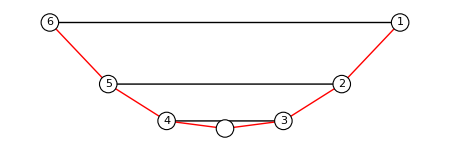
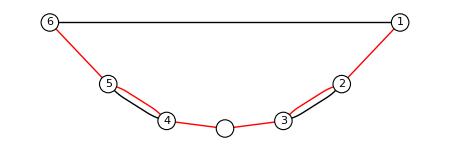
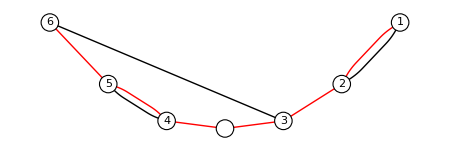
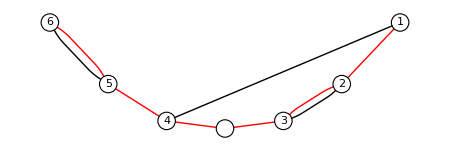
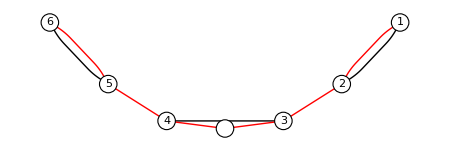
{{-Graphics-,-1/κ^3 8 ⅈ π^3 Μ^2 Ν^2 n_1·(n^–)_6 n_3·(n^–)_4 n_5·(n^–)_2 η_1·γ^σ_3·(η^–)_6 η_3·γ^σ_2·(η^–)_4 η_5·γ^σ_1·(η^–)_2 d_x_2^σ_1[Δ[x_2,x_5]] d_x_4^σ_2[Δ[x_4,x_3]] d_x_6^σ_3[Δ[x_6,x_1]] mod[(ẋ)_1] mod[(ẋ)_2] mod[(ẋ)_3] mod[(ẋ)_4] mod[(ẋ)_5] mod[(ẋ)_6]},{-Graphics-,1/κ^3 8 ⅈ π^3 Μ Ν^3 n_1·(n^–)_6 n_3·(n^–)_2 n_5·(n^–)_4 η_1·γ^σ_3·(η^–)_6 η_3·γ^σ_1·(η^–)_2 η_5·γ^σ_2·(η^–)_4 d_x_2^σ_1[Δ[x_2,x_3]] d_x_4^σ_2[Δ[x_4,x_5]] d_x_6^σ_3[Δ[x_6,x_1]] mod[(ẋ)_1] mod[(ẋ)_2] mod[(ẋ)_3] mod[(ẋ)_4] mod[(ẋ)_5] mod[(ẋ)_6]},{-Graphics-,-1/κ^3 8 ⅈ π^3 Μ^2 Ν^2 n_1·(n^–)_2 n_3·(n^–)_6 n_5·(n^–)_4 η_1·γ^σ_1·(η^–)_2 η_3·γ^σ_3·(η^–)_6 η_5·γ^σ_2·(η^–)_4 d_x_2^σ_1[Δ[x_2,x_1]] d_x_4^σ_2[Δ[x_4,x_5]] d_x_6^σ_3[Δ[x_6,x_3]] mod[(ẋ)_1] mod[(ẋ)_2] mod[(ẋ)_3] mod[(ẋ)_4] mod[(ẋ)_5] mod[(ẋ)_6]},{-Graphics-,-1/κ^3 8 ⅈ π^3 Μ^2 Ν^2 n_1·(n^–)_4 n_3·(n^–)_2 n_5·(n^–)_6 η_1·γ^σ_1·(η^–)_4 η_3·γ^σ_2·(η^–)_2 η_5·γ^σ_3·(η^–)_6 d_x_2^σ_2[Δ[x_2,x_3]] d_x_4^σ_1[Δ[x_4,x_1]] d_x_6^σ_3[Δ[x_6,x_5]] mod[(ẋ)_1] mod[(ẋ)_2] mod[(ẋ)_3] mod[(ẋ)_4] mod[(ẋ)_5] mod[(ẋ)_6]},{-Graphics-,1/κ^3 8 ⅈ π^3 Μ^3 Ν n_1·(n^–)_2 n_3·(n^–)_4 n_5·(n^–)_6 η_1·γ^σ_1·(η^–)_2 η_3·γ^σ_2·(η^–)_4 η_5·γ^σ_3·(η^–)_6 d_x_2^σ_1[Δ[x_2,x_1]] d_x_4^σ_2[Δ[x_4,x_3]] d_x_6^σ_3[Δ[x_6,x_5]] mod[(ẋ)_1] mod[(ẋ)_2] mod[(ẋ)_3] mod[(ẋ)_4] mod[(ẋ)_5] mod[(ẋ)_6]}}

```mathematica
OutFermionic=
```

### Ladder Diagrams 1 (L_1)

```mathematica
OutFermionic[[1]]
```

{-Graphics-,-1/κ^3 8 ⅈ π^3 Μ^2 Ν^2 n_1·(n^–)_6 n_3·(n^–)_4 n_5·(n^–)_2 η_1·γ^σ_3·(η^–)_6 η_3·γ^σ_2·(η^–)_4 η_5·γ^σ_1·(η^–)_2 d_x_2^σ_1[Δ[x_2,x_5]] d_x_4^σ_2[Δ[x_4,x_3]] d_x_6^σ_3[Δ[x_6,x_1]] mod[(ẋ)_1] mod[(ẋ)_2] mod[(ẋ)_3] mod[(ẋ)_4] mod[(ẋ)_5] mod[(ẋ)_6]}

```mathematica
(* We express positions x, velocities xp, propagators Δ, spinors η and bilinears η·γ·ηb in terms of the parameters τ. The value of the product nb·n depends on the position of the cusp (it can be 1 or Cos[θ/2]). *)
```

```mathematica
Ladder1=OutFermionic[[1]][[2]]/.η[x[τ[a_]]]·γ[μ_]·ηb[x[τ[b_]]]:>-2/(η[x[τ[b]]]·ηb[x[τ[a]]])(xp[τ[a],μ]+xp[τ[b],μ])/.d[x[τ[a_]],ξ_,Δ[x[τ[a_]],x[τ[b_]]]]:>- Gamma[3/2-ϵ]/(2 π^(3/2-ϵ))(x[τ[a],ξ]-x[τ[b],ξ])/(((x[τ[a]]-x[τ[b]])^2)^(3/2-ϵ))//.(xp[τ[a_],μ_]+xp[τ[b_],μ_])(x[τ[a_],μ_]-x[τ[b_],μ_]):>2(τ[a]-τ[b])//.(x[τ[a_]]-x[τ[b_]])^2:>(τ[a]-τ[b])^2/.η[x[τ[b_]]]·ηb[x[τ[a_]]]:>2I/.mod[a_]:>1
```

1/κ^3 8 π^(-3/2+3 ϵ) Μ^2 Ν^2 n_1·(n^–)_6 n_3·(n^–)_4 n_5·(n^–)_2 Gamma[3/2-ϵ]^3 (-τ[3]+τ[4]) ((-τ[3]+τ[4])^2)^(-3/2+ϵ) (τ[2]-τ[5]) ((τ[2]-τ[5])^2)^(-3/2+ϵ) (-τ[1]+τ[6]) ((-τ[1]+τ[6])^2)^(-3/2+ϵ)

#### Ladder1 with cusp between τ_4 and τ_3

```mathematica
(* We substitute the value of nb·n for the current case. We perform the change of variable τ->Lτ and we flip the edge with negative τ. Notice that we have introduced the scale μ to keep the action dimensionless in the DRED scheme. *)
```

```mathematica
Ladder1/.nJ[τ[a_]]·nJb[τ[b_]]:>Cos[θ/2]//FullSimplify[#,Assumptions->{τ[1]>τ[2]>τ[3]>0,τ[6]<τ[5]<τ[4]<0}]&;
Ladder11=(μ^(6ϵ)L^6(%/.τ[a_]:>L τ[a]/.τ[4]->-τ[4]/.τ[5]->-τ[5]/.τ[6]->-τ[6])//FullSimplify//PowerExpand//Simplify)/.(a_+b_)^(-2+2ϵ):>((a+b)^2)^(-1+ϵ)
```

(8 L^(6 ϵ) π^(-3/2+3 ϵ) μ^(6 ϵ) Μ^2 Ν^2 Cos[θ/2]^3 Gamma[3/2-ϵ]^3 ((τ[3]+τ[4])^2)^(-1+ϵ) ((τ[2]+τ[5])^2)^(-1+ϵ) ((τ[1]+τ[6])^2)^(-1+ϵ))/κ^3

```mathematica
(* We perform 4 integrals and then we split the result in order to integrate the remaining two variables in the most efficient way. This split the result in 4 parts. *)
```

```mathematica
Integrate[Ladder11,{τ[3],0,τ[2]},{τ[4],0,τ[5]},{τ[1],τ[2],1},{τ[6],τ[5],1},Assumptions->{ϵ>0,0<τ[5]<1,0<τ[2]<1}]//Simplify[#,Assumptions->{ϵ>0,0<τ[5]<1,0<τ[2]<1}]&
Ladder11list=List@@(%//Expand//PowerExpand);
```

1/((1-2 ϵ)^2 ϵ^2 κ^3 (τ[2]+τ[5])^2)2 L^(6 ϵ) π^(-3/2+3 ϵ) μ^(6 ϵ) Μ^2 Ν^2 Cos[θ/2]^3 Gamma[3/2-ϵ]^3 (4^ϵ-(1+τ[2])^(2 ϵ)-(1+τ[5])^(2 ϵ)+(τ[2]+τ[5])^(2 ϵ)) ((τ[2]+τ[5])^(4 ϵ)-(τ[2] (τ[2]+τ[5]))^(2 ϵ)-(τ[5] (τ[2]+τ[5]))^(2 ϵ))

```mathematica
Ladder11p1=Integrate[Ladder11list[[1]]+Ladder11list[[2]]+Ladder11list[[7]]+Ladder11list[[8]]+Ladder11list[[9]],{τ[2],0,1},{τ[5],0,1},Assumptions->{ϵ>1/2}]
```

1/(6 ϵ^3 (-1+2 ϵ)^3 (-1+2 ϵ+8 ϵ^2) κ^3)L^(6 ϵ) π^(-3/2+3 ϵ) μ^(6 ϵ) Μ^2 Ν^2 Cos[θ/2]^3 Gamma[3/2-ϵ]^3 (24 ϵ^2 Hypergeometric2F1[1-4 ϵ,1+2 ϵ,2 (1+ϵ),-1]-3 4^(1+ϵ) ϵ (-1+4 ϵ) Hypergeometric2F1[1-2 ϵ,1+2 ϵ,2 (1+ϵ),-1]+(1+2 ϵ) (-4+3 4^ϵ-64^ϵ+2 (4+64^ϵ) ϵ-6 ϵ Hypergeometric2F1[-2 ϵ,4 ϵ,1+4 ϵ,-1]))

```mathematica
Ladder11p2=Integrate[Ladder11list[[3]]+Ladder11list[[6]]+Ladder11list[[10]]+Ladder11list[[11]]+Ladder11list[[12]],{τ[5],0,1},{τ[2],0,1},Assumptions->{ϵ>1/2}]
```

-((2 L^(6 ϵ) π^(-3/2+3 ϵ) μ^(6 ϵ) Μ^2 Ν^2 Cos[θ/2]^3 Gamma[3/2-ϵ]^3 (1/3 (1-2 ϵ)+1/3 (-1+64^ϵ) (-1+2 ϵ)-(2 ϵ (-1+6 ϵ) Hypergeometric2F1[1-4 ϵ,1+2 ϵ,2 (1+ϵ),-1])/(1+2 ϵ)-1/4 (-1+6 ϵ) (4^ϵ (4-1/ϵ)-2 Hypergeometric2F1[-2 ϵ,4 ϵ,1+4 ϵ,-1])+4^ϵ (-1+4 ϵ) (-1+6 ϵ) Gamma[1+2 ϵ] Hypergeometric2F1Regularized[1-2 ϵ,1+2 ϵ,2 (1+ϵ),-1]))/((1-2 ϵ)^2 ϵ^2 (-1+2 ϵ) (-1+4 ϵ) (-1+6 ϵ) κ^3))

```mathematica
Integrate[Ladder11list[[4]],{τ[5],0,1},Assumptions->{ϵ>1/2,1>τ[2]>0}]/.Hypergeometric2F1[a_,b_,c_,z_]:>(1-z)^-a Hypergeometric2F1[a,c-b,c,z/(z-1)]//FullSimplify[#,Assumptions->{ϵ>1/2,0<τ[2]<1}]&;
Ladder11p3=Integrate[%,{τ[2],0,1},Assumptions->{ϵ>1/2}]
```

-1/κ^3 L^(6 ϵ) π^(-3/2+3 ϵ) (-1+2 ϵ) μ^(6 ϵ) Μ^2 Ν^2 Cos[θ/2]^3 Gamma[1/2-ϵ]^3 Gamma[-4 ϵ] Gamma[2 ϵ] (16^ϵ HypergeometricPFQRegularized[{1,1-4 ϵ,2-2 ϵ},{2-4 ϵ,2+2 ϵ},1/2]-2 HypergeometricPFQRegularized[{1,1-4 ϵ,2-2 ϵ},{2-4 ϵ,2+2 ϵ},1])

```mathematica
Integrate[Ladder11list[[5]],{τ[2],0,1},Assumptions->{ϵ>1/2,1>τ[5]>0}]/.Hypergeometric2F1[a_,b_,c_,z_]:>(1-z)^-a Hypergeometric2F1[a,c-b,c,z/(z-1)]//FullSimplify[#,Assumptions->{ϵ>1/2,0<τ[5]<1}]&;
Ladder11p4=Integrate[%,{τ[5],0,1},Assumptions->{ϵ>1/2}]
```

-1/κ^3 L^(6 ϵ) π^(-3/2+3 ϵ) (-1+2 ϵ) μ^(6 ϵ) Μ^2 Ν^2 Cos[θ/2]^3 Gamma[1/2-ϵ]^3 Gamma[-4 ϵ] Gamma[2 ϵ] (16^ϵ HypergeometricPFQRegularized[{1,1-4 ϵ,2-2 ϵ},{2-4 ϵ,2+2 ϵ},1/2]-2 HypergeometricPFQRegularized[{1,1-4 ϵ,2-2 ϵ},{2-4 ϵ,2+2 ϵ},1])

```mathematica
(* Summing up the four results we have *)
```

```mathematica
Ladder11fin=(Ladder11p1+Ladder11p2+Ladder11p3+Ladder11p4//FunctionExpand//Collect[#,{Hypergeometric2F1[__],HypergeometricPFQ[__]}]&)//Quiet//Simplify
```

1/(384 ϵ^3 (-1+4 ϵ) (-1+6 ϵ) κ^3)L^(6 ϵ) π^(-3/2+3 ϵ) (1+2 ϵ)^2 μ^(6 ϵ) Μ^2 Ν^2 Cos[θ/2]^3 Gamma[-1/2-ϵ]^3 (4+64^ϵ-32 ϵ-2^(1+6 ϵ) ϵ-3 4^(1+ϵ) ϵ-16 ϵ^2+3 4^(2+ϵ) ϵ^2-4^(1+3 ϵ) ϵ^2+128 ϵ^3+9 4^(2+ϵ) ϵ^3+8^(1+2 ϵ) ϵ^3+48 ϵ^2 (-1+6 ϵ) Hypergeometric2F1[1-4 ϵ,1+2 ϵ,2 (1+ϵ),-1]-3 2^(3+2 ϵ) ϵ (1-10 ϵ+24 ϵ^2) Hypergeometric2F1[1-2 ϵ,1+2 ϵ,2 (1+ϵ),-1]-12 ϵ (-1+4 ϵ+12 ϵ^2) Hypergeometric2F1[-2 ϵ,4 ϵ,1+4 ϵ,-1]+3 4^(1+2 ϵ) ϵ (1-8 ϵ+12 ϵ^2) HypergeometricPFQ[{1,1-4 ϵ,2-2 ϵ},{2-4 ϵ,2+2 ϵ},1/2]-24 ϵ (1-8 ϵ+12 ϵ^2) HypergeometricPFQ[{1,1-4 ϵ,2-2 ϵ},{2-4 ϵ,2+2 ϵ},1])

```mathematica
(* Here we expand the result in ϵ up to O(ϵ) order. We leave g[ϵ] outside as in the paper. *)
```

```mathematica
Ladder11exp=g[ϵ]^3 Normal[Series[(Ladder11fin/g[ϵ]^3//PowerExpand)/.Hypergeometric2F1[a_,b_,c_,z_]:>HypExp[Hypergeometric2F1[a,b,c,z],ϵ,3]/.HypergeometricPFQ[{a_,b_,c_},{d_,e_},z_]:>HypExp[HypergeometricPFQ[{a,b,c},{d,e},z],ϵ,3],{ϵ,0,0},Assumptions->ϵ>0]//FullSimplify]//Collect[#,Μ^2 Ν^2 Cos[θ/2]^3]&
```

1/κ^3 π^(-3/2+3 ϵ) (L μ)^(6 ϵ) Μ^2 Ν^2 Cos[θ/2]^3 Gamma[1/2-ϵ]^3 (1/(48 ϵ^3)-(2+Log[4])/(16 ϵ^2)+(-4+2 π^2+3 (Log[2]^2+Log[64]))/(24 ϵ)+1/12 (16+3 Log[2]^2 (1+Log[2])-π^2 (4+Log[4])+Log[4096]-39 Zeta[3]))

```mathematica
(* In the following we will repeat the same structure of this section for any possible position of the cusp. The only change will be the value of nb·n and the intermediate steps of the computations. *)
```

#### Ladder1 with cusp between τ_5 and τ_4

```mathematica
Ladder1/.nJ[τ[3]]·nJb[τ[4]]:>1/.nJ[τ[a_]]·nJb[τ[b_]]:>Cos[θ/2]//FullSimplify[#,Assumptions->{τ[1]>τ[2]>τ[3]>τ[4]>0,τ[6]<τ[5]<0}]&;
Ladder12=(μ^(6ϵ)L^6(%/.τ[a_]:>L τ[a]/.τ[5]->-τ[5]/.τ[6]->-τ[6])//FullSimplify//PowerExpand//Simplify)/.(a_+b_)^(-2+2ϵ):>((a+b)^2)^(-1+ϵ)
```

(8 L^(6 ϵ) π^(-3/2+3 ϵ) μ^(6 ϵ) Μ^2 Ν^2 Cos[θ/2]^2 Gamma[3/2-ϵ]^3 ((τ[3]-τ[4])^2)^(-1+ϵ) ((τ[2]+τ[5])^2)^(-1+ϵ) ((τ[1]+τ[6])^2)^(-1+ϵ))/κ^3

```mathematica
Integrate[Ladder12,{τ[3],0,τ[2]},{τ[4],0,τ[3]},{τ[1],τ[2],1},{τ[6],τ[5],1},Assumptions->{ϵ>1/2,0<τ[5]<1,0<τ[2]<1}]/.(1+Cos[θ]):>2 Cos[θ/2]^2
Ladder12list=List@@(%//Expand);
```

(2 L^(6 ϵ) π^(-3/2+3 ϵ) μ^(6 ϵ) Μ^2 Ν^2 Cos[θ/2]^2 Gamma[3/2-ϵ]^3 τ[2]^(2 ϵ) (τ[2]+τ[5])^(-2+2 ϵ) (4^ϵ-(1+τ[2])^(2 ϵ)-(1+τ[5])^(2 ϵ)+(τ[2]+τ[5])^(2 ϵ)))/((1-2 ϵ)^2 ϵ^2 κ^3)

```mathematica
(Integrate[Ladder12list[[1]]+Ladder12list[[2]]+Ladder12list[[4]],{τ[5],0,1},Assumptions->{ϵ>0,0<τ[2]<1}]//FunctionExpand[#,Assumptions->{ϵ>0,0<τ[2]<1}]&)//FullSimplify;
Integrate[%,τ[2]];
Ladder12p1=((%/.τ[2]->1)-(%/.τ[2]->0)//Simplify[#,Assumptions->{ϵ>0}]&)
```

-1/(48 ϵ^3 (-1+2 ϵ+8 ϵ^2) κ^3)L^(6 ϵ) π^(-3/2+3 ϵ) μ^(6 ϵ) Μ^2 Ν^2 Cos[θ/2]^2 Gamma[1/2-ϵ]^3 (-24 ϵ^2 Hypergeometric2F1[1-4 ϵ,1+2 ϵ,2+2 ϵ,-1]+3 4^(1+ϵ) ϵ (-1+4 ϵ) Hypergeometric2F1[1-2 ϵ,1+2 ϵ,2+2 ϵ,-1]-(1+2 ϵ) (-2-3 4^ϵ+4 (1+3 4^ϵ) ϵ+(3-12 ϵ) Hypergeometric2F1[-2 ϵ,4 ϵ,1+4 ϵ,-1]))

```mathematica
Integrate[Ladder12list[[3]],{τ[2],0,1},Assumptions->{ϵ>1/2,0<τ[5]<1}]/.Hypergeometric2F1[a_,b_,c_,z_]:>(1-z)^-a Hypergeometric2F1[a,c-b,c,z/(z-1)]//FullSimplify[#,Assumptions->{ϵ>1/2,0<τ[5]<1}]&;
Ladder12p2=Integrate[%,{τ[5],0,1},Assumptions->{ϵ>1/2}]/.(1+Cos[θ]) :>2 Cos[θ/2]^2
```

-1/((1-2 ϵ)^2 ϵ κ^3)4 L^(6 ϵ) π^(-3/2+3 ϵ) μ^(6 ϵ) Μ^2 Ν^2 Cos[θ/2]^2 Gamma[3/2-ϵ]^3 Gamma[-4 ϵ] Gamma[1+2 ϵ] (16^ϵ HypergeometricPFQRegularized[{1,1-4 ϵ,2-2 ϵ},{2-4 ϵ,2+2 ϵ},1/2]-2 HypergeometricPFQRegularized[{1,1-4 ϵ,2-2 ϵ},{2-4 ϵ,2+2 ϵ},1])

```mathematica
Ladder12fin=(Ladder12p1+Ladder12p2//FunctionExpand)//Simplify
```

1/(48 ϵ^3 (-1+2 ϵ+8 ϵ^2) κ^3)L^(6 ϵ) π^(-3/2+3 ϵ) μ^(6 ϵ) Μ^2 Ν^2 Cos[θ/2]^2 Gamma[1/2-ϵ]^3 (-2-3 4^ϵ+3 2^(1+2 ϵ) ϵ+8 ϵ^2+3 2^(3+2 ϵ) ϵ^2+24 ϵ^2 Hypergeometric2F1[1-4 ϵ,1+2 ϵ,2 (1+ϵ),-1]+3 4^(1+ϵ) ϵ Hypergeometric2F1[1-2 ϵ,1+2 ϵ,2 (1+ϵ),-1]-3 4^(2+ϵ) ϵ^2 Hypergeometric2F1[1-2 ϵ,1+2 ϵ,2 (1+ϵ),-1]+3 Hypergeometric2F1[-2 ϵ,4 ϵ,1+4 ϵ,-1]-6 ϵ Hypergeometric2F1[-2 ϵ,4 ϵ,1+4 ϵ,-1]-24 ϵ^2 Hypergeometric2F1[-2 ϵ,4 ϵ,1+4 ϵ,-1]+3 2^(1+4 ϵ) ϵ (-1+2 ϵ) HypergeometricPFQ[{1,1-4 ϵ,2-2 ϵ},{2-4 ϵ,2+2 ϵ},1/2]+12 (1-2 ϵ) ϵ HypergeometricPFQ[{1,1-4 ϵ,2-2 ϵ},{2-4 ϵ,2+2 ϵ},1])

```mathematica
Ladder12exp=g[ϵ]^3 Normal[Series[(Ladder12fin/g[ϵ]^3//PowerExpand)/.Hypergeometric2F1[a_,b_,c_,z_]:>HypExp[Hypergeometric2F1[a,b,c,z],ϵ,3]/.HypergeometricPFQ[{a_,b_,c_},{d_,e_},z_]:>HypExp[HypergeometricPFQ[{a,b,c},{d,e},z],ϵ,3],{ϵ,0,0},Assumptions->ϵ>0]//FullSimplify]/.(1+Cos[θ]) :>2 Cos[θ/2]^2//Collect[#,Μ^2 Ν^2 Cos[θ/2]^2]&
```

1/κ^3 π^(-3/2+3 ϵ) (L μ)^(6 ϵ) Μ^2 Ν^2 Cos[θ/2]^2 Gamma[1/2-ϵ]^3 (-1/(48 ϵ^3)+(2+Log[8])/(24 ϵ^2)-(-8+2 π^2+3 Log[2]^2+Log[4096])/(24 ϵ)+1/12 (16+π^2 (1+Log[2])-Log[2] (24+Log[2] (12+Log[32]))+36 Zeta[3]))

#### Ladder1 with cusp between τ_6 and τ_5

```mathematica
Ladder1/.nJ[τ[3]]·nJb[τ[4]]:>1/.nJ[τ[5]]·nJb[τ[2]]:>1/.nJ[τ[a_]]·nJb[τ[b_]]:>Cos[θ/2]//FullSimplify[#,Assumptions->{τ[1]>τ[2]>τ[3]>τ[4]>τ[5]>0,τ[6]<0}]&;
Ladder13=(μ^(6ϵ)L^6(%/.τ[a_]:>L τ[a]/.τ[6]->-τ[6])//FullSimplify//PowerExpand//Simplify)/.(a_+b_)^(-2+2ϵ):>((a+b)^2)^(-1+ϵ)
```

(8 L^(6 ϵ) π^(-3/2+3 ϵ) μ^(6 ϵ) Μ^2 Ν^2 Cos[θ/2] Gamma[3/2-ϵ]^3 ((τ[3]-τ[4])^2)^(-1+ϵ) ((τ[2]-τ[5])^2)^(-1+ϵ) ((τ[1]+τ[6])^2)^(-1+ϵ))/κ^3

```mathematica
Ladder13fin=Integrate[Ladder13,{τ[2],0,1},{τ[5],0,τ[2]},{τ[3],τ[5],τ[2]},{τ[4],τ[5],τ[3]},{τ[1],τ[2],1},{τ[6],0,1},Assumptions->{ϵ>1/2}]
```

(L^(6 ϵ) π^(-3/2+3 ϵ) μ^(6 ϵ) Μ^2 Ν^2 Cos[θ/2] Gamma[3/2-ϵ]^3 (-1+3 4^ϵ-3 Hypergeometric2F1[-2 ϵ,4 ϵ,1+4 ϵ,-1]))/(6 (1-2 ϵ)^2 ϵ^3 (-1+4 ϵ) κ^3)

```mathematica
Ladder13exp=g[ϵ]^3 Normal[Series[(Ladder13fin/g[ϵ]^3//PowerExpand)/.Hypergeometric2F1[a_,b_,c_,z_]:>HypExp[Hypergeometric2F1[a,b,c,z],ϵ,3],{ϵ,0,0},Assumptions->ϵ>0]//FullSimplify]//Collect[#,Μ^2 Ν^2 Cos[θ/2]]&
```

(π^(-3/2+3 ϵ) (L μ)^(6 ϵ) Μ^2 Ν^2 Cos[θ/2] Gamma[1/2-ϵ]^3 (1/(48 ϵ^3)+(4+π^2-3 (Log[2]^2+Log[4]))/(24 ϵ)-(-1+Log[8])/(24 ϵ^2)+1/24 (16+2 π^2-2 Log[2] (12+Log[2]^2+Log[8])-33 Zeta[3])))/κ^3

#### Ladder1 with cusp between -L and τ_6

```mathematica
Ladder1/.nJ[τ[a_]]·nJb[τ[b_]]:>1//FullSimplify[#,Assumptions->{τ[1]>τ[2]>τ[3]>τ[4]>τ[5]>τ[6]>0}]&;
Ladder14=(μ^(6ϵ)L^6(%/.τ[a_]:>L τ[a])//FullSimplify//PowerExpand//Simplify)/.(a_+b_)^(-2+2ϵ):>((a+b)^2)^(-1+ϵ)
```

(8 L^(6 ϵ) π^(-3/2+3 ϵ) μ^(6 ϵ) Μ^2 Ν^2 Gamma[3/2-ϵ]^3 ((τ[3]-τ[4])^2)^(-1+ϵ) ((τ[2]-τ[5])^2)^(-1+ϵ) ((τ[1]-τ[6])^2)^(-1+ϵ))/κ^3

```mathematica
Ladder14fin=Integrate[Integrate[Ladder14,{τ[5],0,τ[2]},{τ[3],τ[5],τ[2]},{τ[4],τ[5],τ[3]},{τ[1],τ[2],1},{τ[6],0,τ[5]},Assumptions->{ϵ>1/2,0<τ[2]<1}],{τ[2],0,1},Assumptions->ϵ>1/2]
```

(L^(6 ϵ) π^(-3/2+3 ϵ) μ^(6 ϵ) Μ^2 Ν^2 Gamma[3/2-ϵ]^3)/(6 ϵ^3 (-1+12 ϵ-44 ϵ^2+48 ϵ^3) κ^3)

```mathematica
Ladder14exp=g[ϵ]^3 Normal[Series[(Ladder14fin/g[ϵ]^3//PowerExpand),{ϵ,0,0},Assumptions->ϵ>0]//FullSimplify]//Collect[#,Μ^2 Ν^2]&
```

(π^(-3/2+3 ϵ) (-16/3-1/(48 ϵ^3)-1/(8 ϵ^2)-5/(6 ϵ)) (L μ)^(6 ϵ) Μ^2 Ν^2 Gamma[1/2-ϵ]^3)/κ^3

#### Summing up

```mathematica
(* The final result is clearly the sum of all the contributions above with their symmetry factors. L1 contains the exact result in terms of Hypergeometric functions,L1exp contains the ϵ expansion up to order O(ϵ). *)
```

```mathematica
L1=Ladder11fin+2Ladder12fin+2Ladder13fin+2Ladder14fin;
```

```mathematica
L1exp=Μ^2 Ν^2 g[ϵ]^3(Series[(Ladder11exp+2Ladder12exp+2Ladder13exp+2Ladder14exp)/(Μ^2 Ν^2 g[ϵ]^3)/.Log[a_]:>With[{f=FactorInteger[a]//Flatten},f[[2]]Log[f[[1]]]]/.Cos[θ/2]:>cθ/.Log[2]->l,{ϵ,0,0}]//Simplify//FullSimplify//Normal)
```

1/κ^3 π^(-3/2+3 ϵ) (L μ)^(6 ϵ) Μ^2 Ν^2 Gamma[1/2-ϵ]^3 ((-2+cθ (2+(-2+cθ) cθ))/(48 ϵ^3)+(-6+cθ (2-6 l+cθ (4+6 l-3 cθ (1+l))))/(24 ϵ^2)+(-40+2 cθ (4-3 l (2+l)+π^2)-2 cθ^2 (3 l (4+l)+2 (-4+π^2))+cθ^3 (3 l (6+l)+2 (-2+π^2)))/(24 ϵ)+1/12 (-128+cθ (16-2 l (12+l (3+l))+2 π^2+cθ^2 (16+3 l (4+l+l^2)-4 π^2-2 l π^2-39 Zeta[3])-33 Zeta[3]+2 cθ (16+π^2+l (-24-l (12+5 l)+π^2)+36 Zeta[3]))))

```mathematica
(* In the following we will follow the same structure for any diagram. We will comment the most importnt steps. *)
```

### Ladder Diagrams 2 (L_2)

```mathematica
OutFermionic[[2]]
```

{-Graphics-,1/κ^3 8 ⅈ π^3 Μ Ν^3 n_1·(n^–)_6 n_3·(n^–)_2 n_5·(n^–)_4 η_1·γ^σ_3·(η^–)_6 η_3·γ^σ_1·(η^–)_2 η_5·γ^σ_2·(η^–)_4 d_x_2^σ_1[Δ[x_2,x_3]] d_x_4^σ_2[Δ[x_4,x_5]] d_x_6^σ_3[Δ[x_6,x_1]] mod[(ẋ)_1] mod[(ẋ)_2] mod[(ẋ)_3] mod[(ẋ)_4] mod[(ẋ)_5] mod[(ẋ)_6]}

```mathematica
Ladder2=OutFermionic[[2]][[2]]/.η[x[τ[a_]]]·γ[μ_]·ηb[x[τ[b_]]]:>-2/(η[x[τ[b]]]·ηb[x[τ[a]]])(xp[τ[a],μ]+xp[τ[b],μ])/.d[x[τ[a_]],ξ_,Δ[x[τ[a_]],x[τ[b_]]]]:>- Gamma[3/2-ϵ]/(2 π^(3/2-ϵ))(x[τ[a],ξ]-x[τ[b],ξ])/(((x[τ[a]]-x[τ[b]])^2)^(3/2-ϵ))//.(xp[τ[a_],μ_]+xp[τ[b_],μ_])(x[τ[a_],μ_]-x[τ[b_],μ_]):>2(τ[a]-τ[b])//.(x[τ[a_]]-x[τ[b_]])^2:>(τ[a]-τ[b])^2/.η[x[τ[b_]]]·ηb[x[τ[a_]]]:>2I/.mod[a_]:>1
```

-1/κ^3 8 π^(-3/2+3 ϵ) Μ Ν^3 n_1·(n^–)_6 n_3·(n^–)_2 n_5·(n^–)_4 Gamma[3/2-ϵ]^3 (τ[2]-τ[3]) ((τ[2]-τ[3])^2)^(-3/2+ϵ) (τ[4]-τ[5]) ((τ[4]-τ[5])^2)^(-3/2+ϵ) (-τ[1]+τ[6]) ((-τ[1]+τ[6])^2)^(-3/2+ϵ)

#### Ladder2 with cusp between τ_4 and τ_3

```mathematica
Ladder2/.nJ[τ[5]]·nJb[τ[4]]:>1/.nJ[τ[3]]·nJb[τ[2]]:>1/.nJ[τ[a_]]·nJb[τ[b_]]:>Cos[θ/2]//FullSimplify[#,Assumptions->{τ[1]>τ[2]>τ[3]>0,τ[6]<τ[5]<τ[4]<0}]&;
Ladder21=(μ^(6ϵ)L^6(%/.τ[a_]:>L τ[a]/.τ[4]->-τ[4]/.τ[5]->-τ[5]/.τ[6]->-τ[6])//FullSimplify//PowerExpand//Simplify)/.(a_+b_)^(-2+2ϵ):>((a+b)^2)^(-1+ϵ)/.(a_+b_)^(2 (-1+ϵ)):>((a+b)^2)^(-1+ϵ)
```

(8 L^(6 ϵ) π^(-3/2+3 ϵ) μ^(6 ϵ) Μ Ν^3 Cos[θ/2] Gamma[3/2-ϵ]^3 ((τ[2]-τ[3])^2)^(-1+ϵ) ((-τ[4]+τ[5])^2)^(-1+ϵ) ((τ[1]+τ[6])^2)^(-1+ϵ))/κ^3

```mathematica
Integrate[Ladder21,{τ[2],0,τ[1]},{τ[3],0,τ[2]},{τ[5],0,τ[6]},{τ[4],0,τ[5]},Assumptions->{ϵ>1/2,0<τ[1]<1,0<τ[6]<1}];
Integrate[%,{τ[1],0,1},Assumptions->{ϵ>1/2,0<τ[6]<1}]/.Hypergeometric2F1[a_,b_,c_,z_]:>(Gamma[c]Gamma[b-a])/(Gamma[b]Gamma[c-a])(-z)^-a Hypergeometric2F1[a,a+1-c,a+1-b,1/z]+(Gamma[c]Gamma[a-b])/(Gamma[a]Gamma[c-b])(-z)^-b Hypergeometric2F1[b,b+1-c,b+1-a,1/z]//FullSimplify[#,Assumptions->{ϵ>1/2,0<τ[6]<1}]&;
Ladder21fin=Integrate[%,{τ[6],0,1},Assumptions->ϵ>1/2]
```

1/(24 ϵ^3 κ^3)L^(6 ϵ) π^(-3/2+3 ϵ) μ^(6 ϵ) Μ Ν^3 Cos[θ/2] Gamma[1/2-ϵ]^3 (-((-1+2 ϵ) ((1+2 ϵ) Hypergeometric2F1[1-4 ϵ,2-2 ϵ,2-4 ϵ,-1]+(-1+4 ϵ) Hypergeometric2F1[2-2 ϵ,1+2 ϵ,2 (1+ϵ),-1]))/(-1+2 ϵ+8 ϵ^2)+(2^(1-4 ϵ) √π ϵ Gamma[2 ϵ] Sec[2 π ϵ])/Gamma[1/2+2 ϵ])

```mathematica
Ladder21exp=g[ϵ]^3 Normal[Series[(Ladder21fin/g[ϵ]^3//PowerExpand)/.Hypergeometric2F1[a_,b_,c_,z_]:>HypExp[Hypergeometric2F1[a,b,c,z],ϵ,3],{ϵ,0,0},Assumptions->ϵ>0]//FullSimplify]//Collect[#,Μ Ν^3 Cos[θ/2]]&
```

(π^(-3/2+3 ϵ) (L μ)^(6 ϵ) Μ Ν^3 Cos[θ/2] Gamma[1/2-ϵ]^3 (1/(24 ϵ^3)-Log[2]/(4 ϵ^2)+(2 π^2-9 Log[2]^2)/(36 ϵ)+1/6 (-Log[2]^3-5 Zeta[3])))/κ^3

#### Ladder2 with cusp between τ_5 and τ_4

```mathematica
Ladder2/.nJ[τ[3]]·nJb[τ[2]]:>1/.nJ[τ[a_]]·nJb[τ[b_]]:>Cos[θ/2]//FullSimplify[#,Assumptions->{τ[1]>τ[2]>τ[3]>τ[4]>0,τ[6]<τ[5]<0}]&;
Ladder22=(μ^(6ϵ)L^6(%/.τ[a_]:>L τ[a]/.τ[5]->-τ[5]/.τ[6]->-τ[6])//FullSimplify//PowerExpand//Simplify)
```

(8 L^(6 ϵ) π^(-3/2+3 ϵ) μ^(6 ϵ) Μ Ν^3 Cos[θ/2]^2 Gamma[3/2-ϵ]^3 (τ[2]-τ[3])^(-2+2 ϵ) (τ[4]+τ[5])^(-2+2 ϵ) (τ[1]+τ[6])^(-2+2 ϵ))/κ^3

```mathematica
Integrate[Ladder22,{τ[5],0,τ[6]},{τ[2],τ[4],τ[1]},{τ[3],τ[4],τ[2]},Assumptions->{0<τ[6]<1,0<τ[4]<τ[1]<1,ϵ>1/2}]/.(1+Cos[θ]):>2 Cos[θ/2]^2
Ladder22list=List@@(%//Expand[#,1]&);
```

(4 L^(6 ϵ) π^(-3/2+3 ϵ) μ^(6 ϵ) Μ Ν^3 Cos[θ/2]^2 Gamma[3/2-ϵ]^3 (τ[1]-τ[4])^(2 ϵ) (-(τ[4] (τ[1]+τ[6]))^(2 ϵ) (τ[4]+τ[6])+τ[4] ((τ[1]+τ[6]) (τ[4]+τ[6]))^(2 ϵ)))/((1-2 ϵ)^2 ϵ κ^3 τ[4] (τ[1]+τ[6])^2 (τ[4]+τ[6]))

```mathematica
Ladder22p1=(Integrate[Ladder22list[[1]],{τ[1],0,1},{τ[4],0,τ[1]},{τ[6],0,1},Assumptions->ϵ>1/2]//FullSimplify)/.Beta[z_,a_,b_]:>(z^a/a) HypergeometricPFQ[{a,1-b},{a+1},z]//FunctionExpand
```

-(2^(-4-2 ϵ) L^(6 ϵ) π^(1/2+3 ϵ) μ^(6 ϵ) Μ Ν^3 (1+Cos[θ]) Csc[2 π ϵ] Gamma[1/2-ϵ]^2 (-1-4 ϵ+6 ϵ Hypergeometric2F1[1-2 ϵ,1+4 ϵ,2+4 ϵ,-1]))/(3 ϵ^3 κ^3 Gamma[-ϵ] Gamma[3/2+2 ϵ])

```mathematica
Integrate[Ladder22list[[2]]/.τ[1]->τ[1]+τ[4]/.τ[6]->τ[6]-τ[4],{τ[1],0,1-τ[4]},Assumptions->{ϵ>1/2,0<τ[4]<1,τ[4]<τ[6]<1+τ[4]}];
Ladder22list2=List@@(Integrate[%,{τ[6],τ[4],1+τ[4]},Assumptions->{ϵ>1/2,0<τ[4]<1}]//Expand[#,2]&)
```

{(4 L^(6 ϵ) π^(-3/2+3 ϵ) μ^(6 ϵ) Μ Ν^3 Cos[θ/2]^2 Gamma[2-4 ϵ] Gamma[3/2-ϵ]^3 Gamma[2 (1+ϵ)] Hypergeometric2F1[2-4 ϵ,2-2 ϵ,3-4 ϵ,1-1/τ[4]] (1-τ[4])^(1+2 ϵ) τ[4]^(-2+4 ϵ))/((1-2 ϵ)^2 ϵ (1+2 ϵ) (-1+6 ϵ) κ^3 Gamma[3-4 ϵ] Gamma[1+2 ϵ]),-(4 L^(6 ϵ) π^(-3/2+3 ϵ) μ^(6 ϵ) Μ Ν^3 Cos[θ/2]^2 Gamma[3/2-ϵ]^3 Hypergeometric2F1[2-2 ϵ,1+2 ϵ,2 (1+ϵ),1-1/τ[4]] (1-τ[4])^(1+2 ϵ) τ[4]^(-2+4 ϵ))/((1-2 ϵ)^2 ϵ (1+2 ϵ) (-1+6 ϵ) κ^3),-((4 L^(6 ϵ) π^(-3/2+3 ϵ) μ^(6 ϵ) Μ Ν^3 Cos[θ/2]^2 Gamma[2-4 ϵ] Gamma[3/2-ϵ]^3 Gamma[2 (1+ϵ)] Hypergeometric2F1[2-4 ϵ,2-2 ϵ,3-4 ϵ,(-1+τ[4])/(1+τ[4])] (1-τ[4])^(1+2 ϵ) (1+τ[4])^(-2+4 ϵ))/((1-2 ϵ)^2 ϵ (1+2 ϵ) (-1+6 ϵ) κ^3 Gamma[3-4 ϵ] Gamma[1+2 ϵ])),(4 L^(6 ϵ) π^(-3/2+3 ϵ) μ^(6 ϵ) Μ Ν^3 Cos[θ/2]^2 Gamma[3/2-ϵ]^3 Hypergeometric2F1[2-2 ϵ,1+2 ϵ,2 (1+ϵ),(-1+τ[4])/(1+τ[4])] (1-τ[4])^(1+2 ϵ) (1+τ[4])^(-2+4 ϵ))/((1-2 ϵ)^2 ϵ (1+2 ϵ) (-1+6 ϵ) κ^3)}

```mathematica
Ladder22list2[[1]]/.Hypergeometric2F1[a_,b_,c_,z_]:>(Gamma[c]Gamma[c-a-b])/(Gamma[c-a]Gamma[c-b])Hypergeometric2F1[a,b,a+b-c+1,1-z]+(1-z)^(c-a-b)(Gamma[c]Gamma[a+b-c])/(Gamma[a]Gamma[b])Hypergeometric2F1[c-a,c-b,c-a-b+1,1-z]/.Hypergeometric2F1[a_,b_,c_,z_]:>(Gamma[b-a]Gamma[c])/(Gamma[b]Gamma[c-a])(-z)^-a Hypergeometric2F1[a,a+1-c,a+1-b,1/z]+(Gamma[a-b]Gamma[c])/(Gamma[a]Gamma[c-b])(-z)^-b Hypergeometric2F1[b,b+1-c,b+1-a,1/z]//Simplify[#,Assumptions->{ϵ>1/2,0<τ[4]<1}]&;
Ladder22p21=Integrate[%,{τ[4],0,1},Assumptions->{ϵ>1/2}]//FullSimplify
```

(16^(-1-ϵ) L^(6 ϵ) π^(3 ϵ) μ^(6 ϵ) Μ Ν^3 Cos[θ/2]^2 Csc[2 π ϵ] Gamma[1/2-ϵ]^3 (1-4 ϵ^2+(-1+16 ϵ^2) Sec[2 π ϵ]))/(3 ϵ^3 (-1+6 ϵ) κ^3 Gamma[-2 ϵ] Gamma[3/2+2 ϵ])

```mathematica
Ladder22list2[[2]]/.Hypergeometric2F1[a_,b_,c_,z_]:>(Gamma[c-a-b]Gamma[c])/(Gamma[c-a]Gamma[c-b])Hypergeometric2F1[a,b,a+b-c+1,1-z]+(1-z)^(c-a-b)(Gamma[a+b-c]Gamma[c])/(Gamma[a]Gamma[b])Hypergeometric2F1[c-a,c-b,c-a-b+1,1-z]//FullSimplify[#,Assumptions->{ϵ>1/2,0<τ[4]<1}]&;
%/.Hypergeometric2F1Regularized[a_,b_,c_,z_]:>Gamma[b-a]/(Gamma[b]Gamma[c-a])(-z)^-a Hypergeometric2F1[a,a+1-c,a+1-b,1/z]+Gamma[a-b]/(Gamma[a]Gamma[c-b])(-z)^-b Hypergeometric2F1[b,b+1-c,b+1-a,1/z]//FullSimplify[#,Assumptions->{ϵ>1/2,0<τ[4]<1}]&;
Ladder22p22=Integrate[% ,{τ[4],0,1},Assumptions->{ϵ>1/2}]//FullSimplify
```

(2^(-3-4 ϵ) L^(6 ϵ) π^(3 ϵ) (-1+2 ϵ) μ^(6 ϵ) Μ Ν^3 (1+Cos[θ]) Csc[2 π ϵ] Gamma[1/2-ϵ]^3)/(3 ϵ (-1+6 ϵ) κ^3 Gamma[1-2 ϵ] Gamma[3/2+2 ϵ])

```mathematica
Ladder22list2[[3]]/.Hypergeometric2F1[a_,b_,c_,z_]:>(1-z)^-a Hypergeometric2F1[a,c-b,c,z/(z-1)]//FullSimplify[#,Assumptions->{ϵ>1/2,0<τ[4]<1}]&;
Ladder22p23=(Integrate[% ,{τ[4],0,1},Assumptions->{ϵ>1/2}]/.Beta[z_,a_,b_]:>(z^a/a) HypergeometricPFQ[{a,1-b},{a+1},z]//FunctionExpand)/.Hypergeometric2F1[a_,b_,c_,z_]:>(1-z)^-b Hypergeometric2F1[b,c-a,c,z/(z-1)]//FullSimplify
```

1/(3 ϵ^2 (1+ϵ) (-1+6 ϵ) κ^3)2^(-5+2 ϵ) L^(6 ϵ) π^(-3/2+3 ϵ) μ^(6 ϵ) Μ Ν^3 (1+Cos[θ]) Gamma[1/2-ϵ]^3 (-(1+ϵ) Hypergeometric2F1[1,1-2 ϵ,3-4 ϵ,-1]+(1-2 ϵ) Hypergeometric2F1[1,1-2 ϵ,3+2 ϵ,-1])

```mathematica
Ladder22list2[[4]]/.Hypergeometric2F1[a_,b_,c_,z_]:>(1-z)^-b Hypergeometric2F1[b,c-a,c,z/(z-1)]//FullSimplify[#,Assumptions->{ϵ>1/2,0<τ[4]<1}]&;
Ladder22p24=(Integrate[% ,{τ[4],0,1},Assumptions->{ϵ>1/2}]/.Beta[z_,a_,b_]:>(z^a/a) HypergeometricPFQ[{a,1-b},{a+1},z]//FunctionExpand)/.Hypergeometric2F1[a_,b_,c_,z_]:>(1-z)^-a Hypergeometric2F1[a,c-b,c,z/(z-1)]//FullSimplify
```

-1/(3 ϵ (-1+6 ϵ) κ^3 Gamma[3/2+2 ϵ])4^(-2+ϵ) L^(6 ϵ) π^(-3/2+3 ϵ) (-1+2 ϵ) μ^(6 ϵ) Μ Ν^3 (1+Cos[θ]) Gamma[1/2-ϵ]^3 Gamma[2 ϵ] (√π-2 Gamma[3/2+2 ϵ] Hypergeometric2F1Regularized[1,4 ϵ,2 (1+ϵ),-1])

```mathematica
Ladder22p2=Ladder22p21+Ladder22p22+Ladder22p23+Ladder22p24;
```

```mathematica
Ladder22fin=(Ladder22p1+Ladder22p2)//Simplify[#,Assumptions->ϵ>0]&
```

1/(3 ϵ^3 κ^3)2^(-5-4 ϵ) L^(6 ϵ) π^(3 ϵ) μ^(6 ϵ) Μ Ν^3 Gamma[1/2-ϵ]^2 ((4 ϵ^2 (-1+2 ϵ) (1+Cos[θ]) Csc[2 π ϵ] Gamma[1/2-ϵ])/((-1+6 ϵ) Gamma[1-2 ϵ] Gamma[3/2+2 ϵ])-(64^ϵ ϵ (1+Cos[θ]) Gamma[1/2-ϵ] ((1+ϵ) Hypergeometric2F1[1,1-2 ϵ,3-4 ϵ,-1]+(-1+2 ϵ) Hypergeometric2F1[1,1-2 ϵ,3+2 ϵ,-1]))/(π^(3/2) (1+ϵ) (-1+6 ϵ))-(2^(1+2 ϵ) √π (1+Cos[θ]) Csc[2 π ϵ] (-1-4 ϵ+6 ϵ Hypergeometric2F1[1-2 ϵ,1+4 ϵ,2+4 ϵ,-1]))/(Gamma[-ϵ] Gamma[3/2+2 ϵ])-(2^(1+6 ϵ) ϵ^2 (-1+2 ϵ) (1+Cos[θ]) Gamma[1/2-ϵ] Gamma[2 ϵ] (√π-2 Gamma[3/2+2 ϵ] Hypergeometric2F1Regularized[1,4 ϵ,2 (1+ϵ),-1]))/(π^(3/2) (-1+6 ϵ) Gamma[3/2+2 ϵ])+(2 Cos[θ/2]^2 Csc[2 π ϵ] Gamma[1/2-ϵ] (1-4 ϵ^2+(-1+16 ϵ^2) Sec[2 π ϵ]))/((-1+6 ϵ) Gamma[-2 ϵ] Gamma[3/2+2 ϵ]))

```mathematica
Ladder22exp=g[ϵ]^3 Normal[Series[(Ladder22fin/g[ϵ]^3//PowerExpand)/. Hypergeometric2F1Regularized[a_,b_,c_,z_]:> 1/Gamma[c] Hypergeometric2F1[a,b,c,z]/.Hypergeometric2F1[a_,b_,c_,z_]:>HypExp[Hypergeometric2F1[a,b,c,z],ϵ,3],{ϵ,0,0},Assumptions->ϵ>0]//FullSimplify]/.(1+Cos[θ]):>2 Cos[θ/2]^2//Collect[#,Μ Ν^3 Cos[θ/2]^2]&
```

1/κ^3 π^(-3/2+3 ϵ) (L μ)^(6 ϵ) Μ Ν^3 Cos[θ/2]^2 Gamma[1/2-ϵ]^3 (-1/(24 ϵ^3)-(7 π^2+36 (-1+Log[2]))/(72 ϵ)+(1+Log[8])/(12 ϵ^2)+1/36 (-π^2 (2+Log[8])-18 (-6+Log[2]^2 (3+Log[2])+Log[64])+102 Zeta[3]))

#### Ladder2 with cusp between τ_6 and τ_5

```mathematica
Ladder2/.nJ[τ[5]]·nJb[τ[4]]:>1/.nJ[τ[3]]·nJb[τ[2]]:>1/.nJ[τ[a_]]·nJb[τ[b_]]:>Cos[θ/2]//FullSimplify[#,Assumptions->{τ[1]>τ[2]>τ[3]>τ[4]>τ[5]>0,τ[6]<0}]&;
Ladder23=(μ^(6ϵ)L^6(%/.τ[a_]:>L τ[a]/.τ[6]->-τ[6])//FullSimplify//PowerExpand//Simplify)/.(a_+b_)^(-2+2ϵ):>((a+b)^2)^(-1+ϵ)
```

(8 L^(6 ϵ) π^(-3/2+3 ϵ) μ^(6 ϵ) Μ Ν^3 Cos[θ/2] Gamma[3/2-ϵ]^3 ((τ[2]-τ[3])^2)^(-1+ϵ) ((τ[4]-τ[5])^2)^(-1+ϵ) ((τ[1]+τ[6])^2)^(-1+ϵ))/κ^3

```mathematica
Ladder23fin=Integrate[Ladder23,{τ[1],0,1},{τ[4],0,τ[1]},{τ[5],0,τ[4]},{τ[6],0,1},{τ[2],τ[4],τ[1]},{τ[3],τ[4],τ[2]},Assumptions->{ϵ>1/2}]/.Beta[z_,a_,b_]:>(z^a/a) HypergeometricPFQ[{a,1-b},{a+1},z]//FunctionExpand
```

(2^(-3-2 ϵ) L^(6 ϵ) π^(1/2+3 ϵ) μ^(6 ϵ) Μ Ν^3 Cos[θ/2] Csc[2 π ϵ] Gamma[1/2-ϵ]^2 (-1-4 ϵ+6 ϵ Hypergeometric2F1[1-2 ϵ,1+4 ϵ,2+4 ϵ,-1]))/(3 ϵ^3 κ^3 Gamma[-ϵ] Gamma[3/2+2 ϵ])

```mathematica
Ladder23exp=g[ϵ]^3 Normal[Series[(Ladder23fin/g[ϵ]^3//PowerExpand)/.Hypergeometric2F1[a_,b_,c_,z_]:>HypExp[Hypergeometric2F1[a,b,c,z],ϵ,3],{ϵ,0,0},Assumptions->ϵ>0]//FullSimplify]//Collect[#,Μ Ν^3 Cos[θ/2]]&
```

(π^(-3/2+3 ϵ) (L μ)^(6 ϵ) Μ Ν^3 Cos[θ/2] Gamma[1/2-ϵ]^3 (1/(24 ϵ^3)-Log[2]/(4 ϵ^2)+(2 π^2-9 Log[2]^2)/(36 ϵ)+1/12 (-2 Log[2]^3+π^2 Log[4]-25 Zeta[3])))/κ^3

#### Ladder2 with cusp between -L and τ_6

```mathematica
Ladder2/.nJ[τ[a_]]·nJb[τ[b_]]:>1//FullSimplify[#,Assumptions->{τ[1]>τ[2]>τ[3]>τ[4]>τ[5]>τ[6]>0}]&;
Ladder24=(μ^(6ϵ)L^6(%/.τ[a_]:>L τ[a])//FullSimplify//PowerExpand//Simplify)/.(a_+b_)^(-2+2ϵ):>((a+b)^2)^(-1+ϵ)
```

(8 L^(6 ϵ) π^(-3/2+3 ϵ) μ^(6 ϵ) Μ Ν^3 Gamma[3/2-ϵ]^3 ((τ[2]-τ[3])^2)^(-1+ϵ) ((τ[4]-τ[5])^2)^(-1+ϵ) ((τ[1]-τ[6])^2)^(-1+ϵ))/κ^3

```mathematica
Ladder24fin=Integrate[Ladder24,{τ[1],0,1},{τ[6],0,τ[1]},{τ[4],τ[6],τ[1]},{τ[5],τ[6],τ[4]},{τ[2],τ[4],τ[1]},{τ[3],τ[4],τ[2]},Assumptions->{ϵ>1/2}]//FullSimplify
```

(L^(6 ϵ) π^(-1/2+3 ϵ) (-1+2 ϵ) μ^(6 ϵ) Μ Ν^3 Csc[2 π ϵ] Gamma[1/2-ϵ]^3 Gamma[2 ϵ])/(48 ϵ^3 (-1+6 ϵ) κ^3 Gamma[-2 ϵ] Gamma[4 ϵ])

```mathematica
Ladder24exp=g[ϵ]^3 Normal[Series[(Ladder24fin/g[ϵ]^3//PowerExpand)/.Hypergeometric2F1[a_,b_,c_,z_]:>HypExp[Hypergeometric2F1[a,b,c,z],ϵ,3],{ϵ,0,0},Assumptions->ϵ>0]//FullSimplify]//Collect[#,Μ Ν^3]&
```

(π^(-3/2+3 ϵ) (L μ)^(6 ϵ) Μ Ν^3 Gamma[1/2-ϵ]^3 (-1/(24 ϵ^3)-1/(6 ϵ^2)+(-36+π^2)/(36 ϵ)+1/9 (π^2-6 (9+Zeta[3]))))/κ^3

#### Summing up

```mathematica
L2=Ladder21fin+2Ladder23fin+2Ladder22fin+2Ladder24fin;
```

```mathematica
L2exp=Μ Ν^3 g[ϵ]^3(Series[(Ladder21exp+2Ladder23exp+2Ladder22exp+2Ladder24exp)/(Μ Ν^3 g[ϵ]^3)/.Log[a_]:>With[{f=FactorInteger[a]//Flatten},f[[2]]Log[f[[1]]]]/.Cos[θ/2]:>cθ/.Log[2]->l,{ϵ,0,0}]//Simplify//FullSimplify//Normal)
```

1/κ^3 π^(-3/2+3 ϵ) (L μ)^(6 ϵ) Μ Ν^3 Gamma[1/2-ϵ]^3 ((-2+(3-2 cθ) cθ)/(24 ϵ^3)+(-4-9 cθ l+cθ^2 (2+6 l))/(12 ϵ^2)+(-2+π^2/18-1/36 cθ (9 (4 cθ (-1+l)+3 l^2)+(-6+7 cθ) π^2))/ϵ+1/18 (-cθ (9 l^3-6 l π^2+cθ (3 l (36+6 l (3+l)+π^2)+2 (-54+π^2-51 Zeta[3]))+90 Zeta[3])+4 (π^2-6 (9+Zeta[3]))))

### Ladder Diagrams 3 (L_3)

```mathematica
OutFermionic[[3]]
```

{-Graphics-,-1/κ^3 8 ⅈ π^3 Μ^2 Ν^2 n_1·(n^–)_2 n_3·(n^–)_6 n_5·(n^–)_4 η_1·γ^σ_1·(η^–)_2 η_3·γ^σ_3·(η^–)_6 η_5·γ^σ_2·(η^–)_4 d_x_2^σ_1[Δ[x_2,x_1]] d_x_4^σ_2[Δ[x_4,x_5]] d_x_6^σ_3[Δ[x_6,x_3]] mod[(ẋ)_1] mod[(ẋ)_2] mod[(ẋ)_3] mod[(ẋ)_4] mod[(ẋ)_5] mod[(ẋ)_6]}

```mathematica
Ladder3=OutFermionic[[3]][[2]]/.η[x[τ[a_]]]·γ[μ_]·ηb[x[τ[b_]]]:>-2/(η[x[τ[b]]]·ηb[x[τ[a]]])(xp[τ[a],μ]+xp[τ[b],μ])/.d[x[τ[a_]],ξ_,Δ[x[τ[a_]],x[τ[b_]]]]:>- Gamma[3/2-ϵ]/(2 π^(3/2-ϵ))(x[τ[a],ξ]-x[τ[b],ξ])/(((x[τ[a]]-x[τ[b]])^2)^(3/2-ϵ))//.(xp[τ[a_],μ_]+xp[τ[b_],μ_])(x[τ[a_],μ_]-x[τ[b_],μ_]):>2(τ[a]-τ[b])//.(x[τ[a_]]-x[τ[b_]])^2:>(τ[a]-τ[b])^2/.η[x[τ[b_]]]·ηb[x[τ[a_]]]:>2I/.mod[a_]:>1
```

1/κ^3 8 π^(-3/2+3 ϵ) Μ^2 Ν^2 n_1·(n^–)_2 n_3·(n^–)_6 n_5·(n^–)_4 Gamma[3/2-ϵ]^3 (-τ[1]+τ[2]) ((-τ[1]+τ[2])^2)^(-3/2+ϵ) (τ[4]-τ[5]) ((τ[4]-τ[5])^2)^(-3/2+ϵ) (-τ[3]+τ[6]) ((-τ[3]+τ[6])^2)^(-3/2+ϵ)

#### Ladder3 with cusp between τ_4 and τ_3

```mathematica
Ladder3/.nJ[τ[5]]·nJb[τ[4]]:>1/.nJ[τ[1]]·nJb[τ[2]]:>1/.nJ[τ[a_]]·nJb[τ[b_]]:>Cos[θ/2]//FullSimplify[#,Assumptions->{τ[1]>τ[2]>τ[3]>0,τ[6]<τ[5]<τ[4]<0}]&;
Ladder31=(μ^(6ϵ)L^6(%/.τ[a_]:>L τ[a]/.τ[4]->-τ[4]/.τ[5]->-τ[5]/.τ[6]->-τ[6])//FullSimplify//PowerExpand//Simplify)/.(a_+b_)^(-2+2ϵ):>((a+b)^2)^(-1+ϵ)/.(a_+b_)^(2 (-1+ϵ)):>((a+b)^2)^(-1+ϵ)
```

(8 L^(6 ϵ) π^(-3/2+3 ϵ) μ^(6 ϵ) Μ^2 Ν^2 Cos[θ/2] Gamma[3/2-ϵ]^3 ((τ[1]-τ[2])^2)^(-1+ϵ) ((-τ[4]+τ[5])^2)^(-1+ϵ) ((τ[3]+τ[6])^2)^(-1+ϵ))/κ^3

```mathematica
(* it is convenient to symmetrize the integrals Subscript[τ, 4],Subscript[τ, 5] and Subscript[τ, 1],Subscript[τ, 2] *)
```

```mathematica
1/2 Integrate[Ladder31,{τ[4],0,τ[6]},{τ[5],0,τ[6]},Assumptions->{0<τ[6]<1,1>τ[1]>τ[2]>τ[3]>0,ϵ>1/2}]/.((τ[1]-τ[2]) (τ[3]+τ[6]))^(2 (-1+ϵ)):>((τ[1]-τ[2])^2 (τ[3]+τ[6])^2)^(-1+ϵ);
1/2 Integrate[%,{τ[1],τ[3],1},{τ[2],τ[3],1},Assumptions->{0<τ[6]<1,1>τ[3]>0,ϵ>1/2}];
Integrate[%,{τ[3],0,1},Assumptions->{0<τ[6]<1,ϵ>1/2}];
Ladder31fin=Integrate[%,{τ[6],0,1},Assumptions->{ϵ>1/2}]
```

(2 L^(6 ϵ) π^(-3/2+3 ϵ) μ^(6 ϵ) Μ^2 Ν^2 Cos[θ/2] Gamma[3/2-ϵ]^3 ((π Csc[4 π ϵ] Gamma[1+2 ϵ] Gamma[2+2 ϵ])/(Gamma[2-2 ϵ] Gamma[1+6 ϵ])+HypergeometricPFQ[{1,1-4 ϵ,2-2 ϵ},{2-4 ϵ,2+2 ϵ},-1]/(-1+4 ϵ)))/((1-2 ϵ)^2 ϵ^2 (1+2 ϵ) κ^3)

```mathematica
Ladder31exp=g[ϵ]^3 Normal[Series[(Ladder31fin/g[ϵ]^3//PowerExpand)/.HypergeometricPFQ[{a_,b_,c_},{d_,e_},z_]:>HypExp[HypergeometricPFQ[{a,b,c},{d,e},z],ϵ,3],{ϵ,0,0},Assumptions->ϵ>0]//FullSimplify]//Collect[#,Μ^2 Ν^2 Cos[θ/2]]&
```

(π^(-3/2+3 ϵ) (L μ)^(6 ϵ) Μ^2 Ν^2 Cos[θ/2] Gamma[1/2-ϵ]^3 (1/(16 ϵ^3)-Log[2]/(4 ϵ^2)-Log[2]^2/(2 ϵ)+1/6 (π^2 Log[2]-4 Log[2]^3+12 Zeta[3])))/κ^3

#### Ladder3 with cusp between τ_5 and τ_4

```mathematica
Ladder3/.nJ[τ[1]]·nJb[τ[2]]:>1/.nJ[τ[a_]]·nJb[τ[b_]]:>Cos[θ/2]//FullSimplify[#,Assumptions->{τ[1]>τ[2]>τ[3]>τ[4]>0,τ[6]<τ[5]<0}]&;
Ladder32=(μ^(6ϵ)L^6(%/.τ[a_]:>L τ[a]/.τ[5]->-τ[5]/.τ[6]->-τ[6])//FullSimplify//PowerExpand//Simplify)/.(a_+b_)^(-2+2ϵ):>((a+b)^2)^(-1+ϵ)/.(a_+b_)^(2 (-1+ϵ)):>((a+b)^2)^(-1+ϵ)
```

(8 L^(6 ϵ) π^(-3/2+3 ϵ) μ^(6 ϵ) Μ^2 Ν^2 Cos[θ/2]^2 Gamma[3/2-ϵ]^3 ((τ[1]-τ[2])^2)^(-1+ϵ) ((τ[4]+τ[5])^2)^(-1+ϵ) ((τ[3]+τ[6])^2)^(-1+ϵ))/κ^3

```mathematica
Ladder32fin=Integrate[Ladder32,{τ[3],0,1},{τ[6],0,1},{τ[4],0,τ[3]},{τ[5],0,τ[6]},{τ[1],τ[3],1},{τ[2],τ[3],τ[1]},Assumptions->{ϵ>1/2}]
```

-1/((1-2 ϵ)^2 ϵ^2 κ^3)2 L^(6 ϵ) π^(-3/2+3 ϵ) μ^(6 ϵ) Μ^2 Ν^2 Cos[θ/2]^2 Gamma[3/2-ϵ]^3 (-(2 Gamma[1+2 ϵ] Gamma[-2+4 ϵ])/(3 Gamma[6 ϵ])-(π Csc[4 π ϵ] Gamma[1+2 ϵ]^2)/((-1+4 ϵ) Gamma[2-2 ϵ] Gamma[1+6 ϵ])+(4 π ϵ Csc[4 π ϵ] Gamma[1+2 ϵ]^2)/((-1+4 ϵ) Gamma[2-2 ϵ] Gamma[1+6 ϵ])+Hypergeometric2F1[1,1-4 ϵ,2 (1+ϵ),-1]/(1-2 ϵ-8 ϵ^2)-(2^(-4 ϵ) ϵ Cos[2 π ϵ] Gamma[-1/2-2 ϵ] Gamma[-1+2 ϵ] Hypergeometric2F1[1-2 ϵ,1+2 ϵ,2+4 ϵ,-1])/(√π)+HypergeometricPFQ[{1,1-4 ϵ,2-2 ϵ},{2-4 ϵ,2+2 ϵ},-1]/(-1+2 ϵ+8 ϵ^2))

```mathematica
Ladder32exp=g[ϵ]^3 Normal[Series[(Ladder32fin/g[ϵ]^3//PowerExpand)/.Hypergeometric2F1[a_,b_,c_,z_]:>HypExp[Hypergeometric2F1[a,b,c,z],ϵ,3]/.HypergeometricPFQ[{a_,b_,c_},{d_,e_},z_]:>HypExp[HypergeometricPFQ[{a,b,c},{d,e},z],ϵ,3],{ϵ,0,0},Assumptions->ϵ>0]//FullSimplify]/.(1+Cos[θ]):>2 Cos[θ/2]^2//Collect[#,Μ^2 Ν^2 Cos[θ/2]^2]&
```

1/κ^3 π^(-3/2+3 ϵ) (L μ)^(6 ϵ) Μ^2 Ν^2 Cos[θ/2]^2 Gamma[1/2-ϵ]^3 (-1/(16 ϵ^3)+(1+Log[4])/(8 ϵ^2)-(π^2-6 (2+Log[2]^2)+Log[4096])/(24 ϵ)+1/24 (48-4 Log[2] (12+Log[2] (9+Log[2]))-π^2 (2+Log[256])+3 Zeta[3]))

#### Ladder3 with cusp between τ_6 and τ_5

```mathematica
Ladder3/.nJ[τ[5]]·nJb[τ[4]]:>1/.nJ[τ[1]]·nJb[τ[2]]:>1/.nJ[τ[a_]]·nJb[τ[b_]]:>Cos[θ/2]//FullSimplify[#,Assumptions->{τ[1]>τ[2]>τ[3]>τ[4]>τ[5]>0,τ[6]<0}]&;
Ladder33=(μ^(6ϵ)L^6(%/.τ[a_]:>L τ[a]/.τ[6]->-τ[6])//FullSimplify//PowerExpand//Simplify)/.(a_+b_)^(-2+2ϵ):>((a+b)^2)^(-1+ϵ)/.(a_+b_)^(2 (-1+ϵ)):>((a+b)^2)^(-1+ϵ)
```

(8 L^(6 ϵ) π^(-3/2+3 ϵ) μ^(6 ϵ) Μ^2 Ν^2 Cos[θ/2] Gamma[3/2-ϵ]^3 ((τ[1]-τ[2])^2)^(-1+ϵ) ((τ[4]-τ[5])^2)^(-1+ϵ) ((τ[3]+τ[6])^2)^(-1+ϵ))/κ^3

```mathematica
1/2 Integrate[Ladder33,{τ[4],0,τ[3]},Assumptions->{0<τ[6]<1,1>τ[1]>τ[2]>τ[3]>τ[5]>0,ϵ>1/2}];
Integrate[%,{τ[5],0,τ[3]},Assumptions->{0<τ[6]<1,1>τ[1]>τ[2]>τ[3]>0,ϵ>1/2}]/.((τ[1]-τ[2]) (τ[3]+τ[6]))^(2 (-1+ϵ)):>((τ[1]-τ[2])^2 (τ[3]+τ[6])^2)^(-1+ϵ);
1/2 Integrate[%,{τ[1],τ[3],1},{τ[2],τ[3],1},Assumptions->{0<τ[6]<1,1>τ[3]>0,ϵ>1/2}];
Integrate[%,{τ[6],0,1},Assumptions->{1>τ[3]>0,ϵ>1/2}];
Ladder33fin=Integrate[%,{τ[3],0,1},Assumptions->{ϵ>1/2}]
```

-1/(ϵ^2 (-1+2 ϵ)^3 κ^3 Gamma[1+6 ϵ])2 L^(6 ϵ) π^(-2+3 ϵ) μ^(6 ϵ) Μ^2 Ν^2 Cos[θ/2] Gamma[3/2-ϵ]^3 (√π Gamma[4 ϵ] Gamma[1+2 ϵ]+ϵ Cos[2 π ϵ] Gamma[-1/2-2 ϵ] Gamma[2 ϵ] Gamma[1+6 ϵ] Hypergeometric2F1[1+2 ϵ,1+6 ϵ,2+4 ϵ,-1])

```mathematica
Ladder33exp=g[ϵ]^3 Normal[Series[(Ladder33fin/g[ϵ]^3//PowerExpand)/.Hypergeometric2F1[a_,b_,c_,z_]:>HypExp[Hypergeometric2F1[a,b,c,z],ϵ,3],{ϵ,0,0},Assumptions->ϵ>0]//FullSimplify]//Collect[#,Μ^2 Ν^2 Cos[θ/2]]&
```

(π^(-3/2+3 ϵ) (L μ)^(6 ϵ) Μ^2 Ν^2 Cos[θ/2] Gamma[1/2-ϵ]^3 (1/(16 ϵ^3)-Log[2]/(4 ϵ^2)-Log[2]^2/(2 ϵ)+1/12 (-8 Log[2]^3+π^2 Log[32]-3 Zeta[3])))/κ^3

#### Ladder3 with cusp between τ_2 and τ_1

```mathematica
Ladder3/.nJ[τ[5]]·nJb[τ[4]]:>1/.nJ[τ[3]]·nJb[τ[6]]:>1/.nJ[τ[a_]]·nJb[τ[b_]]:>Cos[θ/2]//FullSimplify[#,Assumptions->{τ[1]>0,τ[6]<τ[5]<τ[4]<τ[3]<τ[2]<0}]&;
Ladder34=(μ^(6ϵ)L^6(%/.τ[a_]:>L τ[a]/.τ[6]->-τ[6]/.τ[5]->-τ[5]/.τ[4]->-τ[4]/.τ[3]->-τ[3]/.τ[2]->-τ[2])//FullSimplify//PowerExpand//Simplify)/.(a_+b_)^(-2+2ϵ):>((a+b)^2)^(-1+ϵ)/.(a_+b_)^(2 (-1+ϵ)):>((a+b)^2)^(-1+ϵ)
```

(8 L^(6 ϵ) π^(-3/2+3 ϵ) μ^(6 ϵ) Μ^2 Ν^2 Cos[θ/2] Gamma[3/2-ϵ]^3 ((τ[1]+τ[2])^2)^(-1+ϵ) ((τ[4]-τ[5])^2)^(-1+ϵ) ((τ[3]-τ[6])^2)^(-1+ϵ))/κ^3

```mathematica
Ladder34fin=Integrate[Ladder34,{τ[3],0,1},{τ[6],τ[3],1},{τ[1],0,1},{τ[2],0,τ[3]},{τ[5],τ[3],τ[6]},{τ[4],τ[3],τ[5]},Assumptions->{ϵ>1/2}]
```

-(2 L^(6 ϵ) π^(-3/2+3 ϵ) μ^(6 ϵ) Μ^2 Ν^2 Cos[θ/2] Gamma[3/2-ϵ]^3 ((Gamma[4 ϵ] Gamma[1+2 ϵ])/Gamma[1+6 ϵ]-(-1+Hypergeometric2F1[1,-2 ϵ,1+4 ϵ,-1])/(4 ϵ)))/((1-2 ϵ)^2 ϵ^2 (-1+4 ϵ) κ^3)

```mathematica
Ladder34exp=g[ϵ]^3 Normal[Series[(Ladder34fin/g[ϵ]^3//PowerExpand)/.Hypergeometric2F1[a_,b_,c_,z_]:>HypExp[Hypergeometric2F1[a,b,c,z],ϵ,3],{ϵ,0,0},Assumptions->ϵ>0]//FullSimplify]//Collect[#,Μ^2 Ν^2 Cos[θ/2]]&
```

1/κ^3 π^(-3/2+3 ϵ) (L μ)^(6 ϵ) Μ^2 Ν^2 Cos[θ/2] Gamma[1/2-ϵ]^3 (1/(16 ϵ^3)-(-1+Log[2])/(8 ϵ^2)-(-12+π^2+9 Log[2]^2+Log[64])/(24 ϵ)+1/24 (48-6 Log[2] (4+3 Log[2]^2+Log[8])+π^2 (-2+Log[64])+27 Zeta[3]))

#### Ladder3 with cusp between τ_3 and τ_2

```mathematica
Ladder3/.nJ[τ[a_]]·nJb[τ[b_]]:>1//FullSimplify[#,Assumptions->{τ[1]>τ[2]>0,τ[6]<τ[5]<τ[4]<τ[3]<0}]&;
Ladder35=(μ^(6ϵ)L^6(%/.τ[a_]:>L τ[a]/.τ[6]->-τ[6]/.τ[5]->-τ[5]/.τ[4]->-τ[4]/.τ[3]->-τ[3])//FullSimplify//PowerExpand//Simplify)/.(a_+b_)^(-2+2ϵ):>((a+b)^2)^(-1+ϵ)/.(a_+b_)^(2 (-1+ϵ)):>((a+b)^2)^(-1+ϵ)
```

(8 L^(6 ϵ) π^(-3/2+3 ϵ) μ^(6 ϵ) Μ^2 Ν^2 Gamma[3/2-ϵ]^3 ((τ[1]-τ[2])^2)^(-1+ϵ) ((τ[4]-τ[5])^2)^(-1+ϵ) ((τ[3]-τ[6])^2)^(-1+ϵ))/κ^3

```mathematica
Ladder35fin=Integrate[Ladder35,{τ[3],0,1},{τ[6],τ[3],1},{τ[5],τ[3],τ[6]},{τ[4],τ[3],τ[5]},{τ[1],0,1},{τ[2],0,τ[1]},Assumptions->{ϵ>1/2}]
```

-(L^(6 ϵ) π^(-3/2+3 ϵ) (-1+2 ϵ) μ^(6 ϵ) Μ^2 Ν^2 Gamma[1/2-ϵ]^3)/(16 ϵ^3 (-1+4 ϵ) κ^3)

```mathematica
Ladder35exp=g[ϵ]^3 Normal[Series[(Ladder35fin/g[ϵ]^3//PowerExpand),{ϵ,0,0},Assumptions->ϵ>0]//FullSimplify]//Collect[#,Μ^2 Ν^2]&
```

(π^(-3/2+3 ϵ) (-2-1/(16 ϵ^3)-1/(8 ϵ^2)-1/(2 ϵ)) (L μ)^(6 ϵ) Μ^2 Ν^2 Gamma[1/2-ϵ]^3)/κ^3

#### Ladder3 with cusp between -L and τ_6

```mathematica
Ladder3/.nJ[τ[a_]]·nJb[τ[b_]]:>1//FullSimplify[#,Assumptions->{τ[6]<τ[5]<τ[4]<τ[3]<τ[2]<τ[1]<0}]&;
Ladder36=(μ^(6ϵ)L^6(%/.τ[a_]:>L τ[a])//FullSimplify//PowerExpand//Simplify)/.(a_+b_)^(-2+2ϵ):>((a+b)^2)^(-1+ϵ)
```

(8 L^(6 ϵ) π^(-3/2+3 ϵ) μ^(6 ϵ) Μ^2 Ν^2 Gamma[3/2-ϵ]^3 ((τ[1]-τ[2])^2)^(-1+ϵ) ((τ[4]-τ[5])^2)^(-1+ϵ) ((τ[3]-τ[6])^2)^(-1+ϵ))/κ^3

```mathematica
Ladder36fin=Integrate[Ladder36,{τ[3],0,1},{τ[6],0,τ[3]},{τ[4],τ[6],τ[3]},{τ[5],τ[6],τ[4]},{τ[1],τ[3],1},{τ[2],τ[3],τ[1]},Assumptions->{ϵ>1/2}]
```

-(L^(6 ϵ) π^(-3/2+3 ϵ) (-1+2 ϵ) μ^(6 ϵ) Μ^2 Ν^2 Gamma[1/2-ϵ]^3 Gamma[2 ϵ] Gamma[-1+4 ϵ])/(12 ϵ^2 κ^3 Gamma[6 ϵ])

```mathematica
Ladder36exp=g[ϵ]^3 Normal[Series[(Ladder36fin/g[ϵ]^3//PowerExpand),{ϵ,0,0},Assumptions->ϵ>0]//FullSimplify]//Collect[#,Μ^2 Ν^2]&
```

(π^(-3/2+3 ϵ) (L μ)^(6 ϵ) Μ^2 Ν^2 Gamma[1/2-ϵ]^3 (-1/(16 ϵ^3)-1/(8 ϵ^2)+(-6+π^2)/(12 ϵ)+1/6 (-12+π^2+9 PolyGamma[2,1])))/κ^3

#### Summing up

```mathematica
L3=Ladder32fin+Ladder31fin+Ladder33fin+Ladder34fin+Ladder35fin+2 Ladder36fin;
```

```mathematica
L3exp=Μ^2 Ν^2 g[ϵ]^3(Series[(Ladder32exp+Ladder31exp+Ladder33exp+Ladder34exp+Ladder35exp+2 Ladder36exp)/(Μ^2 Ν^2 g[ϵ]^3)/.Log[a_]:>With[{f=FactorInteger[a]//Flatten},f[[2]]Log[f[[1]]]]/.Cos[θ/2]:>cθ/.Log[2]->l,{ϵ,0,0}]//Simplify//FullSimplify//Normal)
```

1/κ^3 π^(-3/2+3 ϵ) (L μ)^(6 ϵ) Μ^2 Ν^2 Gamma[1/2-ϵ]^3 ((-3-(-3+cθ) cθ)/(16 ϵ^3)+(-3+cθ+cθ^2+cθ (-5+2 cθ) l)/(8 ϵ^2)+(-36+3 cθ (4-l (2+11 l)+2 cθ (2+(-2+l) l))-(-4+cθ+cθ^2) π^2)/(24 ϵ)+1/24 (-144+8 π^2-2 cθ (-24+π^2+l (12+l (9+25 l)-10 π^2)+cθ (-24+π^2+2 l (l (9+l)+2 (6+π^2))))+3 (-48+cθ (23+cθ)) Zeta[3]))

### Ladder Diagrams 4 (L_4)

```mathematica
OutFermionic[[4]]
```

{-Graphics-,-1/κ^3 8 ⅈ π^3 Μ^2 Ν^2 n_1·(n^–)_4 n_3·(n^–)_2 n_5·(n^–)_6 η_1·γ^σ_1·(η^–)_4 η_3·γ^σ_2·(η^–)_2 η_5·γ^σ_3·(η^–)_6 d_x_2^σ_2[Δ[x_2,x_3]] d_x_4^σ_1[Δ[x_4,x_1]] d_x_6^σ_3[Δ[x_6,x_5]] mod[(ẋ)_1] mod[(ẋ)_2] mod[(ẋ)_3] mod[(ẋ)_4] mod[(ẋ)_5] mod[(ẋ)_6]}

```mathematica
(* It's the same of Subscript[L, 3] *)
```

### Ladder Diagrams 5 (L_5)

```mathematica
OutFermionic[[5]]
```

{-Graphics-,1/κ^3 8 ⅈ π^3 Μ^3 Ν n_1·(n^–)_2 n_3·(n^–)_4 n_5·(n^–)_6 η_1·γ^σ_1·(η^–)_2 η_3·γ^σ_2·(η^–)_4 η_5·γ^σ_3·(η^–)_6 d_x_2^σ_1[Δ[x_2,x_1]] d_x_4^σ_2[Δ[x_4,x_3]] d_x_6^σ_3[Δ[x_6,x_5]] mod[(ẋ)_1] mod[(ẋ)_2] mod[(ẋ)_3] mod[(ẋ)_4] mod[(ẋ)_5] mod[(ẋ)_6]}

```mathematica
Ladder5=OutFermionic[[5]][[2]]/.η[x[τ[a_]]]·γ[μ_]·ηb[x[τ[b_]]]:>-2/(η[x[τ[b]]]·ηb[x[τ[a]]])(xp[τ[a],μ]+xp[τ[b],μ])/.d[x[τ[a_]],ξ_,Δ[x[τ[a_]],x[τ[b_]]]]:>- Gamma[3/2-ϵ]/(2 π^(3/2-ϵ))(x[τ[a],ξ]-x[τ[b],ξ])/(((x[τ[a]]-x[τ[b]])^2)^(3/2-ϵ))//.(xp[τ[a_],μ_]+xp[τ[b_],μ_])(x[τ[a_],μ_]-x[τ[b_],μ_]):>2(τ[a]-τ[b])//.(x[τ[a_]]-x[τ[b_]])^2:>(τ[a]-τ[b])^2/.η[x[τ[b_]]]·ηb[x[τ[a_]]]:>2I/.mod[a_]:>1
```

-1/κ^3 8 π^(-3/2+3 ϵ) Μ^3 Ν n_1·(n^–)_2 n_3·(n^–)_4 n_5·(n^–)_6 Gamma[3/2-ϵ]^3 (-τ[1]+τ[2]) ((-τ[1]+τ[2])^2)^(-3/2+ϵ) (-τ[3]+τ[4]) ((-τ[3]+τ[4])^2)^(-3/2+ϵ) (-τ[5]+τ[6]) ((-τ[5]+τ[6])^2)^(-3/2+ϵ)

#### Ladder5 with cusp between τ_4 and τ_3

```mathematica
Ladder5/.nJ[τ[5]]·nJb[τ[6]]:>1/.nJ[τ[1]]·nJb[τ[2]]:>1/.nJ[τ[a_]]·nJb[τ[b_]]:>Cos[θ/2]//FullSimplify[#,Assumptions->{τ[1]>τ[2]>τ[3]>0,τ[6]<τ[5]<τ[4]<0}]&;
Ladder51=(μ^(6ϵ)L^6(%/.τ[a_]:>L τ[a]/.τ[4]->-τ[4]/.τ[5]->-τ[5]/.τ[6]->-τ[6])//FullSimplify//PowerExpand//Simplify)/.(a_+b_)^(-2+2ϵ):>((a+b)^2)^(-1+ϵ)/.(a_+b_)^(2 (-1+ϵ)):>((a+b)^2)^(-1+ϵ)
```

(8 L^(6 ϵ) π^(-3/2+3 ϵ) μ^(6 ϵ) Μ^3 Ν Cos[θ/2] Gamma[3/2-ϵ]^3 ((τ[1]-τ[2])^2)^(-1+ϵ) ((τ[3]+τ[4])^2)^(-1+ϵ) ((-τ[5]+τ[6])^2)^(-1+ϵ))/κ^3

```mathematica
1/2 Integrate[Ladder51,{τ[6],τ[4],1},{τ[5],τ[4],1},Assumptions->{0<τ[4]<1,0<τ[3]<τ[2]<τ[1]<1,ϵ>1/2}]/.((τ[1]-τ[2]) (τ[3]+τ[4]))^(2 (-1+ϵ)):>((τ[1]-τ[2])^2 (τ[3]+τ[4])^2)^(-1+ϵ);
1/2 Integrate[%,{τ[2],τ[3],1},{τ[1],τ[3],1},Assumptions->{0<τ[4]<1,0<τ[3]<1,ϵ>1/2}];
Integrate[%,{τ[4],0,1},Assumptions->{0<τ[3]<1,ϵ>1/2}];
Ladder51fin=Integrate[%,{τ[3],0,1},Assumptions->{ϵ>1/2}]
```

(2^(1-4 ϵ) L^(6 ϵ) π^(3 ϵ) μ^(6 ϵ) Μ^3 Ν Cos[θ/2] Csc[2 π ϵ] Gamma[3/2-ϵ]^3 (-4 ϵ Hypergeometric2F1[1,1-4 ϵ,2 (1+ϵ),-1]+(1+2 ϵ) Hypergeometric2F1[1,-2 ϵ,1+4 ϵ,-1]))/((1-2 ϵ)^2 ϵ^2 (1+2 ϵ) κ^3 Gamma[2-2 ϵ] Gamma[1/2+2 ϵ])

```mathematica
Ladder51exp=g[ϵ]^3 Normal[Series[(Ladder51fin/g[ϵ]^3//PowerExpand)/.Hypergeometric2F1[a_,b_,c_,z_]:>HypExp[Hypergeometric2F1[a,b,c,z],ϵ,3],{ϵ,0,0},Assumptions->ϵ>0]//FullSimplify]//Collect[#,Μ^3 Ν Cos[θ/2]]&
```

(π^(-3/2+3 ϵ) (L μ)^(6 ϵ) Μ^3 Ν Cos[θ/2] Gamma[1/2-ϵ]^3 (1/(8 ϵ^3)-Log[2]/(4 ϵ^2)-(π^2+9 Log[2]^2)/(12 ϵ)+1/6 (π^2 Log[2]-9 Log[2]^3+21 Zeta[3])))/κ^3

#### Ladder5 with cusp between τ_6 and τ_5

```mathematica
Ladder5/.nJ[τ[3]]·nJb[τ[4]]:>1/.nJ[τ[1]]·nJb[τ[2]]:>1/.nJ[τ[a_]]·nJb[τ[b_]]:>Cos[θ/2]//FullSimplify[#,Assumptions->{τ[1]>τ[2]>τ[3]>τ[4]>τ[5]>0,τ[6]<0}]&;
Ladder52=(μ^(6ϵ)L^6(%/.τ[a_]:>L τ[a]/.τ[6]->-τ[6])//FullSimplify//PowerExpand//Simplify)/.(a_+b_)^(-2+2ϵ):>((a+b)^2)^(-1+ϵ)
```

(8 L^(6 ϵ) π^(-3/2+3 ϵ) μ^(6 ϵ) Μ^3 Ν Cos[θ/2] Gamma[3/2-ϵ]^3 ((τ[1]-τ[2])^2)^(-1+ϵ) ((τ[3]-τ[4])^2)^(-1+ϵ) ((τ[5]+τ[6])^2)^(-1+ϵ))/κ^3

```mathematica
1/2 Integrate[Ladder52,{τ[4],τ[5],τ[2]},{τ[3],τ[5],τ[2]},Assumptions->{0<τ[6]<1,1>τ[1]>τ[2]>τ[5]>0,ϵ>1/2}]/.((τ[1]-τ[2]) (τ[5]+τ[6]))^(2 (-1+ϵ)):>((τ[1]-τ[2])^2 (τ[5]+τ[6])^2)^(-1+ϵ);
Integrate[%,{τ[1],τ[2],1},Assumptions->{0<τ[6]<1,1>τ[2]>τ[5]>0,ϵ>1/2}];
Integrate[%,{τ[6],0,1},Assumptions->{1>τ[2]>τ[5]>0,ϵ>1/2}];
Integrate[%,{τ[2],τ[5],1},Assumptions->{1>τ[5]>0,ϵ>1/2}];
Ladder52fin=Integrate[%,{τ[5],0,1},Assumptions->{ϵ>1/2}]//FunctionExpand
```

(L^(6 ϵ) π^(-3/2+3 ϵ) μ^(6 ϵ) Μ^3 Ν Cos[θ/2] Gamma[1/2-ϵ]^3 Gamma[2 ϵ]^3)/(κ^3 Gamma[1+6 ϵ])-(L^(6 ϵ) π^(-3/2+3 ϵ) μ^(6 ϵ) Μ^3 Ν Cos[θ/2] Gamma[1/2-ϵ]^3 Gamma[2 ϵ]^2 Hypergeometric2F1[1,1-2 ϵ,2+4 ϵ,-1])/(κ^3 Gamma[2+4 ϵ])

```mathematica
Ladder52exp=g[ϵ]^3 Normal[Series[(Ladder52fin/g[ϵ]^3//PowerExpand)/.Hypergeometric2F1[a_,b_,c_,z_]:>HypExp[Hypergeometric2F1[a,b,c,z],ϵ,3],{ϵ,0,0},Assumptions->ϵ>0]//FullSimplify]//Collect[#,Μ^3 Ν Cos[θ/2]]&
```

(π^(-3/2+3 ϵ) (L μ)^(6 ϵ) Μ^3 Ν Cos[θ/2] Gamma[1/2-ϵ]^3 (1/(8 ϵ^3)-Log[2]/(4 ϵ^2)-(2 π^2+9 Log[2]^2)/(12 ϵ)+1/12 (8 π^2 Log[2]-18 Log[2]^3+51 Zeta[3])))/κ^3

#### Ladder5 with cusp between τ_5 and τ_4

```mathematica
Ladder5/.nJ[τ[a_]]·nJb[τ[b_]]:>1//FullSimplify[#,Assumptions->{τ[1]>τ[2]>τ[3]>τ[4]>0,τ[6]<τ[5]<0}]&;
Ladder53=(μ^(6ϵ)L^6(%/.τ[a_]:>L τ[a]/.τ[6]->-τ[6]/.τ[5]->-τ[5])//FullSimplify//PowerExpand//Simplify)/.(a_+b_)^(-2+2ϵ):>((a+b)^2)^(-1+ϵ)/.(a_+b_)^(2 (-1+ϵ)):>((a+b)^2)^(-1+ϵ)
```

(8 L^(6 ϵ) π^(-3/2+3 ϵ) μ^(6 ϵ) Μ^3 Ν Gamma[3/2-ϵ]^3 ((τ[1]-τ[2])^2)^(-1+ϵ) ((τ[3]-τ[4])^2)^(-1+ϵ) ((-τ[5]+τ[6])^2)^(-1+ϵ))/κ^3

```mathematica
Integrate[Ladder53,{τ[3],0,τ[2]},{τ[4],0,τ[3]},Assumptions->{0<τ[5]<τ[6]<1,1>τ[1]>τ[2]>0,ϵ>1/2}];
Integrate[%,{τ[6],0,1},{τ[5],0,τ[6]},Assumptions->{1>τ[1]>τ[2]>0,ϵ>1/2}];
Integrate[%,{τ[1],τ[2],1},Assumptions->{1>τ[2]>0,ϵ>1/2}];
Ladder53fin=Integrate[%,{τ[2],0,1},Assumptions->{ϵ>1/2}]
```

-(L^(6 ϵ) π^(-3/2+3 ϵ) μ^(6 ϵ) Μ^3 Ν Gamma[1/2-ϵ]^3 Gamma[2 ϵ] Gamma[1+2 ϵ])/(4 ϵ^2 κ^3 Gamma[1+4 ϵ])

```mathematica
Ladder53exp=g[ϵ]^3 Normal[Series[(Ladder53fin/g[ϵ]^3//PowerExpand),{ϵ,0,0},Assumptions->ϵ>0]//FullSimplify]//Collect[#,Μ^3 Ν]&
```

(π^(-3/2+3 ϵ) (L μ)^(6 ϵ) Μ^3 Ν Gamma[1/2-ϵ]^3 (-1/(8 ϵ^3)+π^2/(12 ϵ)+PolyGamma[2,1]))/κ^3

#### Ladder5 with cusp between -L and τ_6

```mathematica
Ladder5/.nJ[τ[a_]]·nJb[τ[b_]]:>1//FullSimplify[#,Assumptions->{τ[1]>τ[2]>τ[3]>τ[4]>τ[5]>τ[6]>0}]&;
Ladder54=(μ^(6ϵ)L^6(%/.τ[a_]:>L τ[a])//FullSimplify//PowerExpand//Simplify)/.(a_+b_)^(-2+2ϵ):>((a+b)^2)^(-1+ϵ)/.(a_+b_)^(2 (-1+ϵ)):>((a+b)^2)^(-1+ϵ)
```

(8 L^(6 ϵ) π^(-3/2+3 ϵ) μ^(6 ϵ) Μ^3 Ν Gamma[3/2-ϵ]^3 ((τ[1]-τ[2])^2)^(-1+ϵ) ((τ[3]-τ[4])^2)^(-1+ϵ) ((τ[5]-τ[6])^2)^(-1+ϵ))/κ^3

```mathematica
Integrate[Ladder54,{τ[1],τ[3],1},{τ[2],τ[3],τ[1]},Assumptions->{1>τ[1]>τ[2]>τ[3]>τ[4]>0,ϵ>1/2}];
Integrate[%,{τ[5],0,τ[4]},{τ[6],0,τ[5]},Assumptions->{1>τ[3]>τ[4]>0,ϵ>1/2}];
Integrate[%,{τ[3],τ[4],1},Assumptions->{1>τ[4]>0,ϵ>1/2}];
Ladder54fin=Integrate[%,{τ[4],0,1},Assumptions->{ϵ>1/2}]
```

-(L^(6 ϵ) π^(-3/2+3 ϵ) μ^(6 ϵ) Μ^3 Ν Gamma[1/2-ϵ]^3 Gamma[2 ϵ]^3)/(κ^3 Gamma[1+6 ϵ])

```mathematica
Ladder54exp=g[ϵ]^3 Normal[Series[(Ladder54fin/g[ϵ]^3//PowerExpand),{ϵ,0,0},Assumptions->ϵ>0]//FullSimplify]//Collect[#,Μ^3 Ν]&
```

(π^(-3/2+3 ϵ) (L μ)^(6 ϵ) Μ^3 Ν Gamma[1/2-ϵ]^3 (-1/(8 ϵ^3)+π^2/(4 ϵ)-8 Zeta[3]))/κ^3

#### Summing up

```mathematica
L5=Ladder51fin+2Ladder52fin+2Ladder53fin+2 Ladder54fin;
```

```mathematica
L5exp=Μ^3 Ν g[ϵ]^3(Series[(Ladder51exp+2Ladder52exp+2Ladder53exp+2 Ladder54exp)/(Μ^3 Ν g[ϵ]^3)/.Log[a_]:>With[{f=FactorInteger[a]//Flatten},f[[2]]Log[f[[1]]]]/.Cos[θ/2]:>cθ/.Log[2]->l,{ϵ,0,0}]//Simplify//FullSimplify//Normal)
```

(π^(-3/2+3 ϵ) (L μ)^(6 ϵ) Μ^3 Ν Gamma[1/2-ϵ]^3 (3/2 cθ l (-3 l^2+π^2)+(-4+3 cθ)/(8 ϵ^3)-(3 cθ l)/(4 ϵ^2)+(-(9 cθ l^2)/4+1/12 (8-5 cθ) π^2)/ϵ+4 (-5+3 cθ) Zeta[3]))/κ^3

### Total Fermionic contribution

```mathematica
LF=L1+L2+2 L3+L5;
```

```mathematica
LFexp=Μ Ν g[ϵ]^3(Series[(L1exp+L2exp+2 L3exp+L5exp)/(Μ Ν g[ϵ]^3),{ϵ,0,0}]//Simplify//FullSimplify//Normal)
```

1/κ^3 π^(-3/2+3 ϵ) (L μ)^(6 ϵ) Μ Ν Gamma[1/2-ϵ]^3 ((6 (-4+3 cθ) Μ^2+(-20+cθ (20+(-8+cθ) cθ)) Μ Ν-2 (2+cθ (-3+2 cθ)) Ν^2)/(48 ϵ^3)+1/(72 ϵ)(-6 (27 cθ l^2+(-8+5 cθ) π^2) Μ^2+3 (-8 cθ (-4+3 l+9 l^2)+cθ^2 (40+6 (-8+l) l-6 π^2)+8 (-14+π^2)+cθ^3 (3 l (6+l)+2 (-2+π^2))) Μ Ν-2 (9 (8+4 cθ^2 (-1+l)+3 cθ l^2)+(-2+cθ (-6+7 cθ)) π^2) Ν^2)+(-3 cθ^3 (1+l) Μ Ν-8 Ν (3 Μ+Ν)+2 cθ^2 Ν (5 Μ+9 l Μ+2 Ν+6 l Ν)-2 cθ (-4 Μ Ν+9 l (Μ+Ν)^2))/(24 ϵ^2)+1/36 (8 Ν (3 (-34+π^2) Μ+(-54+π^2) Ν)+cθ^2 Ν (-2 Ν (3 l (36+6 l (3+l)+π^2)+2 (-54+π^2-51 Zeta[3]))-3 Μ (-80+2 l (48+30 l+7 l^2+3 π^2)-75 Zeta[3]))+3 cθ^3 Μ Ν (16+3 l (4+l+l^2)-4 π^2-2 l π^2-39 Zeta[3])-48 (15 Μ^2+9 Μ Ν+Ν^2) Zeta[3]+6 cθ (32 Μ Ν-12 l^2 Μ Ν-l^3 (27 Μ^2+26 Μ Ν+3 Ν^2)+l (-24 Μ Ν+π^2 (9 Μ^2+10 Μ Ν+2 Ν^2))+6 (12 Μ^2+3 Μ Ν-5 Ν^2) Zeta[3])))

## Bosonic Ladder diagrams

```mathematica
(* We use the input window of WiLE to compute the integrands of the bosonic ladder diagrams for the cusped Wilson line. Since the only non-vanishing bosonic diagrams contains 1 fermionic propagators and a couple of bosonic propagators, we have to expand the loop in order to have 2 ψ's or ψb's and 2 CCb or CbC. We are interested in planar diagrams than we choos the option "on". The diagrams clearly do not involve tadpoles and self-energies than we turn off the options. *)
```

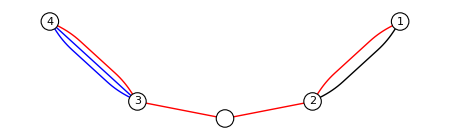
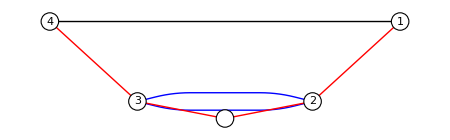
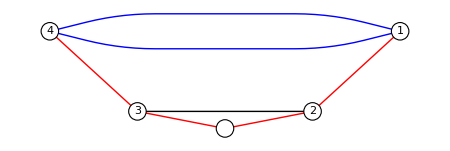
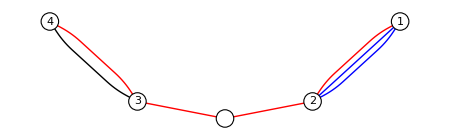
{{-Graphics-,-(8 ⅈ π^3 Μ^2 Ν^2 n_1·(n^–)_2 η_1·γ^σ_1·(η^–)_2 d_x_2^σ_1[Δ[x_2,x_1]] mod[(ẋ)_1] mod[(ẋ)_2] mod[(ẋ)_3] mod[(ẋ)_4] tr[M_3·M_4] Δ[x_3,x_4] Δ[x_4,x_3])/κ^3},{-Graphics-,-(8 ⅈ π^3 Μ^2 Ν^2 n_1·(n^–)_4 η_1·γ^σ_1·(η^–)_4 d_x_4^σ_1[Δ[x_4,x_1]] mod[(ẋ)_1] mod[(ẋ)_2] mod[(ẋ)_3] mod[(ẋ)_4] tr[(M̂)_2·(M̂)_3] Δ[x_2,x_3] Δ[x_3,x_2])/κ^3},{-Graphics-,-(8 ⅈ π^3 Μ^2 Ν^2 n_2·(n^–)_3 η_2·γ^σ_1·(η^–)_3 d_x_3^σ_1[Δ[x_3,x_2]] mod[(ẋ)_1] mod[(ẋ)_2] mod[(ẋ)_3] mod[(ẋ)_4] tr[M_1·M_4] Δ[x_1,x_4] Δ[x_4,x_1])/κ^3},{-Graphics-,-(8 ⅈ π^3 Μ^2 Ν^2 n_3·(n^–)_4 η_3·γ^σ_1·(η^–)_4 d_x_4^σ_1[Δ[x_4,x_3]] mod[(ẋ)_1] mod[(ẋ)_2] mod[(ẋ)_3] mod[(ẋ)_4] tr[M_1·M_2] Δ[x_1,x_2] Δ[x_2,x_1])/κ^3}}

```mathematica
OutBosonic=
```

### Ladder Diagrams 6 (L_6)

```mathematica
OutBosonic[[1]]
```

{-Graphics-,-(8 ⅈ π^3 Μ^2 Ν^2 n_1·(n^–)_2 η_1·γ^σ_1·(η^–)_2 d_x_2^σ_1[Δ[x_2,x_1]] mod[(ẋ)_1] mod[(ẋ)_2] mod[(ẋ)_3] mod[(ẋ)_4] tr[M_3·M_4] Δ[x_3,x_4] Δ[x_4,x_3])/κ^3}

```mathematica
(* We express positions x, velocities xp, propagators Δ, spinors η and bilinears η·γ·ηb in terms of the parameters τ. The value of the products nb·n and M·M depend on the position of the cusp (nb·n can be 1 or Cos[θ/2], M·M can be 4 or 4 Cos[θ/2]^2). *)
```

```mathematica
Ladder6=OutBosonic[[1]][[2]]/.η[x[τ[a_]]]·γ[μ_]·ηb[x[τ[b_]]]:>-2/(η[x[τ[b]]]·ηb[x[τ[a]]])(xp[τ[a],μ]+xp[τ[b],μ])/.d[x[τ[a_]],ξ_,Δ[x[τ[a_]],x[τ[b_]]]]:>- Gamma[3/2-ϵ]/(2 π^(3/2-ϵ))(x[τ[a],ξ]-x[τ[b],ξ])/(((x[τ[a]]-x[τ[b]])^2)^(3/2-ϵ))/.Δ[x[τ[a_]],x[τ[b_]]]:> Gamma[1/2-ϵ]/(4 π^(3/2-ϵ))1/(((x[τ[a]]-x[τ[b]])^2)^(1/2-ϵ))//.(xp[τ[a_],μ_]+xp[τ[b_],μ_])(x[τ[a_],μ_]-x[τ[b_],μ_]):>2(τ[a]-τ[b])//.(x[τ[a_]]-x[τ[b_]])^2:>(τ[a]-τ[b])^2/.η[x[τ[b_]]]·ηb[x[τ[a_]]]:>2I/.mod[a_]:>1
```

-(π^(-3/2+3 ϵ) Μ^2 Ν^2 n_1·(n^–)_2 Gamma[1/2-ϵ]^2 Gamma[3/2-ϵ] tr[M_3·M_4] (-τ[1]+τ[2]) ((-τ[1]+τ[2])^2)^(-3/2+ϵ) ((τ[3]-τ[4])^2)^(-1/2+ϵ) ((-τ[3]+τ[4])^2)^(-1/2+ϵ))/(2 κ^3)

#### Ladder6 with cusp between τ_4 and τ_3

```mathematica
(* We substitute the value of nb·n and M·M for the current case. The other operations are similar to the previous cases. *)
```

```mathematica
Ladder6/.nJ[τ[a_]]·nJb[τ[b_]]:>1/.tr[M[τ[a_]]·M[τ[b_]]]:>4 Cos[θ/2]^2//FullSimplify[#,Assumptions->{τ[1]>τ[2]>τ[3]>0,τ[4]<0}]&;
Ladder61=(μ^(6ϵ)L^4(%/.τ[a_]:>L τ[a]/.τ[4]->-τ[4])//FullSimplify//PowerExpand//Simplify)/.(a_+b_)^(-2+2ϵ):>((a+b)^2)^(-1+ϵ)/.(a_+b_)^(-2+4ϵ):>((a+b)^2)^(-1+2ϵ)
```

(L^(6 ϵ) π^(-3/2+3 ϵ) μ^(6 ϵ) Μ^2 Ν^2 (1+Cos[θ]) Gamma[1/2-ϵ]^2 Gamma[3/2-ϵ] ((τ[1]-τ[2])^2)^(-1+ϵ) ((τ[3]+τ[4])^2)^(-1+2 ϵ))/κ^3

```mathematica
Ladder61fin=Integrate[Ladder61,{τ[2],0,1},{τ[1],τ[2],1},{τ[3],0,τ[2]},{τ[4],0,1},Assumptions->ϵ>1/2]
```

-(L^(6 ϵ) π^(-3/2+3 ϵ) μ^(6 ϵ) Μ^2 Ν^2 (1+Cos[θ]) Gamma[1/2-ϵ]^2 Gamma[3/2-ϵ] ((Gamma[2 ϵ] Gamma[1+4 ϵ])/Gamma[1+6 ϵ]-(-1+Hypergeometric2F1[1,-4 ϵ,1+2 ϵ,-1])/(2 ϵ)))/(4 ϵ (1-6 ϵ+8 ϵ^2) κ^3)

```mathematica
Ladder61exp=g[ϵ]^3 Normal[Series[(Ladder61fin/g[ϵ]^3//PowerExpand)/.Hypergeometric2F1[a_,b_,c_,z_]:>HypExp[Hypergeometric2F1[a,b,c,z],ϵ,3],{ϵ,0,0},Assumptions->ϵ>0]//FullSimplify]/.(1+Cos[θ]):>2 Cos[θ/2]^2//Collect[#,Μ^2 Ν^2 Cos[θ/2]^2]&
```

(π^(-3/2+3 ϵ) (L μ)^(6 ϵ) Μ^2 Ν^2 Cos[θ/2]^2 Gamma[1/2-ϵ]^3 (-1/(8 ϵ^2)+(-1+Log[2])/(2 ϵ)+1/12 (π^2+6 (-4+3 Log[2]^2+Log[16]))))/κ^3

#### Ladder6 with cusp between τ_2 and τ_1

```mathematica
Ladder6/.nJ[τ[a_]]·nJb[τ[b_]]:>Cos[θ/2]/.tr[M[τ[a_]]·M[τ[b_]]]:>4//FullSimplify[#,Assumptions->{τ[1]>0,τ[4]<τ[3]<τ[2]<0}]&;
Ladder62=(μ^(6ϵ)L^4(%/.τ[a_]:>L τ[a]/.τ[4]->-τ[4]/.τ[3]->-τ[3]/.τ[2]->-τ[2])//FullSimplify//PowerExpand//Simplify)/.(a_+b_)^(-2+2ϵ):>((a+b)^2)^(-1+ϵ)/.(a_+b_)^(-2+4ϵ):>((a+b)^2)^(-1+2ϵ)
```

(2 L^(6 ϵ) π^(-3/2+3 ϵ) μ^(6 ϵ) Μ^2 Ν^2 Cos[θ/2] Gamma[1/2-ϵ]^2 Gamma[3/2-ϵ] ((τ[1]+τ[2])^2)^(-1+ϵ) ((-τ[3]+τ[4])^2)^(-1+2 ϵ))/κ^3

```mathematica
Ladder62fin=Integrate[Ladder62,{τ[3],0,1},{τ[2],0,τ[3]},{τ[1],0,1},{τ[4],τ[3],1},Assumptions->ϵ>1/2]
```

-(L^(6 ϵ) π^(-3/2+3 ϵ) μ^(6 ϵ) Μ^2 Ν^2 Cos[θ/2] Gamma[1/2-ϵ]^2 Gamma[3/2-ϵ] ((Gamma[4 ϵ] Gamma[1+2 ϵ])/Gamma[1+6 ϵ]-(-1+Hypergeometric2F1[1,-2 ϵ,1+4 ϵ,-1])/(4 ϵ)))/(ϵ (1-6 ϵ+8 ϵ^2) κ^3)

```mathematica
Ladder62exp=g[ϵ]^3 Normal[Series[(Ladder62fin/g[ϵ]^3//PowerExpand)/.Hypergeometric2F1[a_,b_,c_,z_]:>HypExp[Hypergeometric2F1[a,b,c,z],ϵ,3],{ϵ,0,0},Assumptions->ϵ>0]//FullSimplify]//Collect[#,Μ^2 Ν^2 Cos[θ/2]]&
```

(π^(-3/2+3 ϵ) (L μ)^(6 ϵ) Μ^2 Ν^2 Cos[θ/2] Gamma[1/2-ϵ]^3 (-1/(8 ϵ^2)+(-4+Log[4])/(8 ϵ)+1/12 (-24+π^2+9 Log[2]^2+Log[4096])))/κ^3

#### Ladder6 with cusp between τ_3 and τ_2

```mathematica
Ladder6/.nJ[τ[a_]]·nJb[τ[b_]]:>1/.tr[M[τ[a_]]·M[τ[b_]]]:>4//FullSimplify[#,Assumptions->{τ[1]>τ[2]>0,τ[4]<τ[3]<0}]&;
Ladder63=(μ^(6ϵ)L^4(%/.τ[a_]:>L τ[a]/.τ[4]->-τ[4]/.τ[3]->-τ[3])//FullSimplify//PowerExpand//Simplify)/.(a_+b_)^(-2+2ϵ):>((a+b)^2)^(-1+ϵ)/.(a_+b_)^(-2+4ϵ):>((a+b)^2)^(-1+2ϵ)
```

(2 L^(6 ϵ) π^(-3/2+3 ϵ) μ^(6 ϵ) Μ^2 Ν^2 Gamma[1/2-ϵ]^2 Gamma[3/2-ϵ] ((τ[1]-τ[2])^2)^(-1+ϵ) ((-τ[3]+τ[4])^2)^(-1+2 ϵ))/κ^3

```mathematica
Ladder63fin=Integrate[Ladder63,{τ[1],0,1},{τ[2],0,τ[1]},{τ[4],0,1},{τ[3],0,τ[4]},Assumptions->{ϵ>1/2}]
```

-(L^(6 ϵ) π^(-3/2+3 ϵ) μ^(6 ϵ) Μ^2 Ν^2 Gamma[1/2-ϵ]^3)/(8 ϵ^2 (-1+4 ϵ) κ^3)

```mathematica
Ladder63exp=g[ϵ]^3 Normal[Series[(Ladder63fin/g[ϵ]^3//PowerExpand),{ϵ,0,0},Assumptions->ϵ>0]//FullSimplify]//Collect[#,Μ^2 Ν^2]&
```

(π^(-3/2+3 ϵ) (2+1/(8 ϵ^2)+1/(2 ϵ)) (L μ)^(6 ϵ) Μ^2 Ν^2 Gamma[1/2-ϵ]^3)/κ^3

#### Ladder6 with cusp between -L and τ_4

```mathematica
Ladder6/.nJ[τ[a_]]·nJb[τ[b_]]:>1/.tr[M[τ[a_]]·M[τ[b_]]]:>4//FullSimplify[#,Assumptions->{τ[1]>τ[2]>τ[3]>τ[4]>0}]&;
Ladder64=(μ^(6ϵ)L^4(%/.τ[a_]:>L τ[a])//FullSimplify//PowerExpand//Simplify)/.(a_+b_)^(-2+2ϵ):>((a+b)^2)^(-1+ϵ)/.(a_+b_)^(-2+4ϵ):>((a+b)^2)^(-1+2ϵ)
```

(2 L^(6 ϵ) π^(-3/2+3 ϵ) μ^(6 ϵ) Μ^2 Ν^2 Gamma[1/2-ϵ]^2 Gamma[3/2-ϵ] ((τ[1]-τ[2])^2)^(-1+ϵ) ((τ[3]-τ[4])^2)^(-1+2 ϵ))/κ^3

```mathematica
Ladder64fin=Integrate[Ladder64,{τ[3],0,1},{τ[4],0,τ[3]},{τ[1],τ[3],1},{τ[2],τ[3],τ[1]},Assumptions->{ϵ>1/2}]
```

-(L^(6 ϵ) π^(-3/2+3 ϵ) μ^(6 ϵ) Μ^2 Ν^2 Gamma[1/2-ϵ]^3 Gamma[2 ϵ] Gamma[-1+4 ϵ])/(κ^3 Gamma[1+6 ϵ])

```mathematica
Ladder64exp=g[ϵ]^3 Normal[Series[(Ladder64fin/g[ϵ]^3//PowerExpand),{ϵ,0,0},Assumptions->ϵ>0]//FullSimplify]//Collect[#,Μ^2 Ν^2]&
```

(π^(-3/2+3 ϵ) (1/6 (12-π^2)+1/(8 ϵ^2)+1/(2 ϵ)) (L μ)^(6 ϵ) Μ^2 Ν^2 Gamma[1/2-ϵ]^3)/κ^3

#### Summing up

```mathematica
L6=Ladder61fin+Ladder62fin+Ladder63fin+2 Ladder64fin;
```

```mathematica
L6exp=Μ^2 Ν^2 g[ϵ]^3(Series[(Ladder61exp+Ladder62exp+Ladder63exp+2 Ladder64exp)/(Μ^2 Ν^2 g[ϵ]^3)/.Log[a_]:>With[{f=FactorInteger[a]//Flatten},f[[2]]Log[f[[1]]]]/.Cos[θ/2]:>cθ/.Log[2]->l,{ϵ,0,0}]//Simplify//FullSimplify//Normal)
```

(π^(-3/2+3 ϵ) (1/12 (72+3 cθ (-8+2 cθ (2+l) (-2+3 l)+l (4+3 l))+(-4+cθ+cθ^2) π^2)+(3-cθ (1+cθ))/(8 ϵ^2)+(6+cθ (-2+2 cθ (-1+l)+l))/(4 ϵ)) (L μ)^(6 ϵ) Μ^2 Ν^2 Gamma[1/2-ϵ]^3)/κ^3

### Ladder Diagrams 7 (L_7)

```mathematica
OutBosonic[[2]]
```

{-Graphics-,-(8 ⅈ π^3 Μ^2 Ν^2 n_1·(n^–)_4 η_1·γ^σ_1·(η^–)_4 d_x_4^σ_1[Δ[x_4,x_1]] mod[(ẋ)_1] mod[(ẋ)_2] mod[(ẋ)_3] mod[(ẋ)_4] tr[(M̂)_2·(M̂)_3] Δ[x_2,x_3] Δ[x_3,x_2])/κ^3}

```mathematica
Ladder7=OutBosonic[[2]][[2]]/.η[x[τ[a_]]]·γ[μ_]·ηb[x[τ[b_]]]:>-2/(η[x[τ[b]]]·ηb[x[τ[a]]])(xp[τ[a],μ]+xp[τ[b],μ])/.d[x[τ[a_]],ξ_,Δ[x[τ[a_]],x[τ[b_]]]]:>- Gamma[3/2-ϵ]/(2 π^(3/2-ϵ))(x[τ[a],ξ]-x[τ[b],ξ])/(((x[τ[a]]-x[τ[b]])^2)^(3/2-ϵ))/.Δ[x[τ[a_]],x[τ[b_]]]:> Gamma[1/2-ϵ]/(4 π^(3/2-ϵ))1/(((x[τ[a]]-x[τ[b]])^2)^(1/2-ϵ))//.(xp[τ[a_],μ_]+xp[τ[b_],μ_])(x[τ[a_],μ_]-x[τ[b_],μ_]):>2(τ[a]-τ[b])//.(x[τ[a_]]-x[τ[b_]])^2:>(τ[a]-τ[b])^2/.η[x[τ[b_]]]·ηb[x[τ[a_]]]:>2I/.mod[a_]:>1
```

-(π^(-3/2+3 ϵ) Μ^2 Ν^2 n_1·(n^–)_4 Gamma[1/2-ϵ]^2 Gamma[3/2-ϵ] tr[(M̂)_2·(M̂)_3] ((τ[2]-τ[3])^2)^(-1/2+ϵ) ((-τ[2]+τ[3])^2)^(-1/2+ϵ) (-τ[1]+τ[4]) ((-τ[1]+τ[4])^2)^(-3/2+ϵ))/(2 κ^3)

#### Ladder7 with cusp between τ_3 and τ_2

```mathematica
Ladder7/.nJ[τ[a_]]·nJb[τ[b_]]:>Cos[θ/2]/.tr[Mh[τ[a_]]·Mh[τ[b_]]]:>4 Cos[θ/2]^2//FullSimplify[#,Assumptions->{τ[1]>τ[2]>0,τ[4]<τ[3]<0}]&;
Ladder71=(μ^(6ϵ)L^4(%/.τ[a_]:>L τ[a]/.τ[4]->-τ[4]/.τ[3]->-τ[3])//FullSimplify//PowerExpand//Simplify)/.(a_+b_)^(-2+2ϵ):>((a+b)^2)^(-1+ϵ)/.(a_+b_)^(-2+4ϵ):>((a+b)^2)^(-1+2ϵ)
```

(2 L^(6 ϵ) π^(-3/2+3 ϵ) μ^(6 ϵ) Μ^2 Ν^2 Cos[θ/2]^3 Gamma[1/2-ϵ]^2 Gamma[3/2-ϵ] ((τ[2]+τ[3])^2)^(-1+2 ϵ) ((τ[1]+τ[4])^2)^(-1+ϵ))/κ^3

```mathematica
Integrate[Ladder71,{τ[1],τ[2],1},{τ[4],τ[3],1},Assumptions->{ϵ>1/2,0<τ[3]<1,0<τ[2]<1}]
Ladder71list=List@@(%//Expand);
```

(L^(6 ϵ) π^(-3/2+3 ϵ) μ^(6 ϵ) Μ^2 Ν^2 Cos[θ/2]^3 Gamma[1/2-ϵ]^2 Gamma[3/2-ϵ] (τ[2]+τ[3])^(-2+4 ϵ) (4^ϵ-(1+τ[2])^(2 ϵ)-(1+τ[3])^(2 ϵ)+(τ[2]+τ[3])^(2 ϵ)))/(ϵ (-1+2 ϵ) κ^3)

```mathematica
Integrate[Ladder71list[[2]]+Ladder71list[[1]]+Ladder71list[[4]],τ[3]];
(%/.τ[3]->1)-(%/.τ[3]->0)//Simplify;
Integrate[%,τ[2]];
Ladder71p1=(%/.τ[2]->1)-(%/.τ[2]->0)//Simplify[#,Assumptions->ϵ>0]&
```

(L^(6 ϵ) π^(-3/2+3 ϵ) μ^(6 ϵ) Μ^2 Ν^2 Cos[θ/2]^3 Gamma[1/2-ϵ]^2 Gamma[3/2-ϵ] (2+3 2^(1+2 ϵ)-3 64^ϵ+2 (-2-9 2^(1+2 ϵ)+7 64^ϵ) ϵ+3 (-1+6 ϵ) Hypergeometric2F1[-2 ϵ,4 ϵ,1+4 ϵ,-1]))/(12 ϵ^2 (-1+2 ϵ) (-1+4 ϵ) (-1+6 ϵ) κ^3)

```mathematica
Integrate[Ladder71list[[3]],τ[2]];
(%/.τ[2]->1)-(%/.τ[2]->0)//Simplify;
Integrate[%,τ[3]];
Ladder71p2=(%/.τ[3]->1)-(%/.τ[3]->0)//Simplify[#,Assumptions->ϵ>0]&
```

-(L^(6 ϵ) π^(-3/2+3 ϵ) μ^(6 ϵ) Μ^2 Ν^2 Cos[θ/2]^3 Gamma[1/2-ϵ]^2 Gamma[3/2-ϵ] (2 (-1+64^ϵ)-3 Hypergeometric2F1[-2 ϵ,4 ϵ,1+4 ϵ,-1]))/(12 ϵ^2 (1-6 ϵ+8 ϵ^2) κ^3)

```mathematica
Ladder71fin=Ladder71p1+Ladder71p2//Simplify
```

(L^(6 ϵ) π^(-3/2+3 ϵ) μ^(6 ϵ) Μ^2 Ν^2 Cos[θ/2]^3 Gamma[1/2-ϵ]^2 Gamma[3/2-ϵ] (-4^ϵ (-6+16^ϵ)+2 (4-9 2^(1+2 ϵ)+64^ϵ) ϵ+6 (-1+6 ϵ) Hypergeometric2F1[-2 ϵ,4 ϵ,1+4 ϵ,-1]))/(12 ϵ^2 (-1+2 ϵ) (-1+4 ϵ) (-1+6 ϵ) κ^3)

```mathematica
Ladder71exp=g[ϵ]^3 Normal[Series[(Ladder71fin/g[ϵ]^3//PowerExpand)/.Hypergeometric2F1[a_,b_,c_,z_]:>HypExp[Hypergeometric2F1[a,b,c,z],ϵ,3],{ϵ,0,0},Assumptions->ϵ>0]//FullSimplify]//Collect[#,Μ^2 Ν^2 Cos[θ/2]^3]&
```

(π^(-3/2+3 ϵ) (L μ)^(6 ϵ) Μ^2 Ν^2 Cos[θ/2]^3 Gamma[1/2-ϵ]^3 (1/(24 ϵ^2)-Log[2]/(4 ϵ)+1/12 (2 π^2+3 (-4+Log[2]^2))))/κ^3

#### Ladder7 with cusp between τ_4 and τ_3

```mathematica
Ladder7/.nJ[τ[a_]]·nJb[τ[b_]]:>Cos[θ/2]/.tr[Mh[τ[a_]]·Mh[τ[b_]]]:>4//FullSimplify[#,Assumptions->{τ[1]>τ[2]>τ[3]>0,τ[4]<0}]&;
Ladder72=(μ^(6ϵ)L^4(%/.τ[a_]:>L τ[a]/.τ[4]->-τ[4])//FullSimplify//PowerExpand//Simplify)/.(a_+b_)^(-2+2ϵ):>((a+b)^2)^(-1+ϵ)/.(a_+b_)^(-2+4ϵ):>((a+b)^2)^(-1+2ϵ)
```

(2 L^(6 ϵ) π^(-3/2+3 ϵ) μ^(6 ϵ) Μ^2 Ν^2 Cos[θ/2] Gamma[1/2-ϵ]^2 Gamma[3/2-ϵ] ((τ[2]-τ[3])^2)^(-1+2 ϵ) ((τ[1]+τ[4])^2)^(-1+ϵ))/κ^3

```mathematica
Ladder72fin=Integrate[Ladder72,{τ[2],0,1},{τ[3],0,τ[2]},{τ[1],τ[2],1},{τ[4],0,1},Assumptions->ϵ>1/2]
```

(L^(6 ϵ) π^(-3/2+3 ϵ) μ^(6 ϵ) Μ^2 Ν^2 Cos[θ/2] Gamma[1/2-ϵ]^2 Gamma[3/2-ϵ] (-1+3 4^ϵ-3 Hypergeometric2F1[-2 ϵ,4 ϵ,1+4 ϵ,-1]))/(12 ϵ^2 (1-6 ϵ+8 ϵ^2) κ^3)

```mathematica
Ladder72exp=g[ϵ]^3 Normal[Series[(Ladder72fin/g[ϵ]^3//PowerExpand)/.Hypergeometric2F1[a_,b_,c_,z_]:>HypExp[Hypergeometric2F1[a,b,c,z],ϵ,3],{ϵ,0,0},Assumptions->ϵ>0]//FullSimplify]//Collect[#,Μ^2 Ν^2 Cos[θ/2]]&
```

(π^(-3/2+3 ϵ) (L μ)^(6 ϵ) Μ^2 Ν^2 Cos[θ/2] Gamma[1/2-ϵ]^3 (-1/(24 ϵ^2)+1/48 (-32-4 π^2+3 Log[4] (8+Log[4]))+(-4+Log[64])/(24 ϵ)))/κ^3

#### Ladder7 with cusp between -L and τ_4

```mathematica
Ladder7/.nJ[τ[a_]]·nJb[τ[b_]]:>1/.tr[Mh[τ[a_]]·Mh[τ[b_]]]:>4//FullSimplify[#,Assumptions->{τ[1]>τ[2]>τ[3]>τ[4]>0}]&;
Ladder73=(μ^(6ϵ)L^4(%/.τ[a_]:>L τ[a])//FullSimplify//PowerExpand//Simplify)/.(a_+b_)^(-2+2ϵ):>((a+b)^2)^(-1+ϵ)/.(a_+b_)^(-2+4ϵ):>((a+b)^2)^(-1+2ϵ)
```

(2 L^(6 ϵ) π^(-3/2+3 ϵ) μ^(6 ϵ) Μ^2 Ν^2 Gamma[1/2-ϵ]^2 Gamma[3/2-ϵ] ((τ[2]-τ[3])^2)^(-1+2 ϵ) ((τ[1]-τ[4])^2)^(-1+ϵ))/κ^3

```mathematica
Ladder73fin=Integrate[Ladder73,{τ[4],0,1},{τ[1],τ[4],1},{τ[2],τ[4],τ[1]},{τ[3],τ[4],τ[2]},Assumptions->{ϵ>1/2}]
```

(L^(6 ϵ) π^(-3/2+3 ϵ) μ^(6 ϵ) Μ^2 Ν^2 Gamma[1/2-ϵ]^2 Gamma[3/2-ϵ])/(12 ϵ^2 (-1+4 ϵ) (-1+6 ϵ) κ^3)

```mathematica
Ladder73exp=g[ϵ]^3 Normal[Series[(Ladder73fin/g[ϵ]^3//PowerExpand),{ϵ,0,0},Assumptions->ϵ>0]//FullSimplify]//Collect[#,Μ^2 Ν^2]&
```

(π^(-3/2+3 ϵ) (7/3+1/(24 ϵ^2)+1/(3 ϵ)) (L μ)^(6 ϵ) Μ^2 Ν^2 Gamma[1/2-ϵ]^3)/κ^3

#### Summing up

```mathematica
L7=Ladder71fin+2Ladder72fin+2Ladder73fin;
```

```mathematica
L7exp=Μ^2 Ν^2 g[ϵ]^3(Series[(Ladder71exp+2Ladder72exp+2Ladder73exp)/(Μ^2 Ν^2 g[ϵ]^3)/.Log[a_]:>With[{f=FactorInteger[a]//Flatten},f[[2]]Log[f[[1]]]]/.Cos[θ/2]:>cθ/.Log[2]->l,{ϵ,0,0}]//Simplify//FullSimplify//Normal)
```

(π^(-3/2+3 ϵ) (1/12 (56-2 cθ (8-3 l (4+l)+π^2)+cθ^3 (3 l^2+2 (-6+π^2)))+(2-2 cθ+cθ^3)/(24 ϵ^2)+(8-3 cθ^3 l+cθ (-4+6 l))/(12 ϵ)) (L μ)^(6 ϵ) Μ^2 Ν^2 Gamma[1/2-ϵ]^3)/κ^3

### Ladder Diagrams 8 (L_8)

```mathematica
OutBosonic[[3]]
```

{-Graphics-,-(8 ⅈ π^3 Μ^2 Ν^2 n_2·(n^–)_3 η_2·γ^σ_1·(η^–)_3 d_x_3^σ_1[Δ[x_3,x_2]] mod[(ẋ)_1] mod[(ẋ)_2] mod[(ẋ)_3] mod[(ẋ)_4] tr[M_1·M_4] Δ[x_1,x_4] Δ[x_4,x_1])/κ^3}

```mathematica
Ladder8=OutBosonic[[3]][[2]]/.η[x[τ[a_]]]·γ[μ_]·ηb[x[τ[b_]]]:>-2/(η[x[τ[b]]]·ηb[x[τ[a]]])(xp[τ[a],μ]+xp[τ[b],μ])/.d[x[τ[a_]],ξ_,Δ[x[τ[a_]],x[τ[b_]]]]:>- Gamma[3/2-ϵ]/(2 π^(3/2-ϵ))(x[τ[a],ξ]-x[τ[b],ξ])/(((x[τ[a]]-x[τ[b]])^2)^(3/2-ϵ))/.Δ[x[τ[a_]],x[τ[b_]]]:> Gamma[1/2-ϵ]/(4 π^(3/2-ϵ))1/(((x[τ[a]]-x[τ[b]])^2)^(1/2-ϵ))//.(xp[τ[a_],μ_]+xp[τ[b_],μ_])(x[τ[a_],μ_]-x[τ[b_],μ_]):>2(τ[a]-τ[b])//.(x[τ[a_]]-x[τ[b_]])^2:>(τ[a]-τ[b])^2/.η[x[τ[b_]]]·ηb[x[τ[a_]]]:>2I/.mod[a_]:>1
```

-(π^(-3/2+3 ϵ) Μ^2 Ν^2 n_2·(n^–)_3 Gamma[1/2-ϵ]^2 Gamma[3/2-ϵ] tr[M_1·M_4] (-τ[2]+τ[3]) ((-τ[2]+τ[3])^2)^(-3/2+ϵ) ((τ[1]-τ[4])^2)^(-1/2+ϵ) ((-τ[1]+τ[4])^2)^(-1/2+ϵ))/(2 κ^3)

#### Ladder8 with cusp between τ_3 and τ_2

```mathematica
Ladder8/.nJ[τ[a_]]·nJb[τ[b_]]:>Cos[θ/2]/.tr[M[τ[a_]]·M[τ[b_]]]:>4 Cos[θ/2]^2//FullSimplify[#,Assumptions->{τ[1]>τ[2]>0,τ[4]<τ[3]<0}]&;
Ladder81=(μ^(6ϵ)L^4(%/.τ[a_]:>L τ[a]/.τ[4]->-τ[4]/.τ[3]->-τ[3])//FullSimplify//PowerExpand//Simplify)/.(a_+b_)^(-2+2ϵ):>((a+b)^2)^(-1+ϵ)/.(a_+b_)^(-2+4ϵ):>((a+b)^2)^(-1+2ϵ)
```

(2 L^(6 ϵ) π^(-3/2+3 ϵ) μ^(6 ϵ) Μ^2 Ν^2 Cos[θ/2]^3 Gamma[1/2-ϵ]^2 Gamma[3/2-ϵ] ((τ[2]+τ[3])^2)^(-1+ϵ) ((τ[1]+τ[4])^2)^(-1+2 ϵ))/κ^3

```mathematica
Integrate[Ladder81,{τ[1],τ[2],1},{τ[4],τ[3],1},Assumptions->{ϵ>1/2,0<τ[3]<1,0<τ[2]<1}]
Ladder81list=List@@(%//Expand);
```

(L^(6 ϵ) π^(-3/2+3 ϵ) μ^(6 ϵ) Μ^2 Ν^2 Cos[θ/2]^3 Gamma[1/2-ϵ]^2 Gamma[3/2-ϵ] (τ[2]+τ[3])^(-2+2 ϵ) (16^ϵ-(1+τ[2])^(4 ϵ)-(1+τ[3])^(4 ϵ)+(τ[2]+τ[3])^(4 ϵ)))/(2 ϵ (-1+4 ϵ) κ^3)

```mathematica
Integrate[Ladder81list[[2]]+Ladder81list[[1]]+Ladder81list[[4]],τ[3]];
(%/.τ[3]->1)-(%/.τ[3]->0)//Simplify;
Integrate[%,τ[2]];
Ladder81p1=(%/.τ[2]->1)-(%/.τ[2]->0)//Simplify[#,Assumptions->ϵ>0]&
```

(L^(6 ϵ) π^(-3/2+3 ϵ) μ^(6 ϵ) Μ^2 Ν^2 Cos[θ/2]^3 Gamma[1/2-ϵ]^2 Gamma[3/2-ϵ] (1+3 2^(1+4 ϵ)-3 64^ϵ+2 (1-9 2^(1+4 ϵ)+7 64^ϵ) ϵ+3 (-1+6 ϵ) Hypergeometric2F1[-4 ϵ,2 ϵ,1+2 ϵ,-1]))/(12 ϵ^2 (-1+2 ϵ) (-1+4 ϵ) (-1+6 ϵ) κ^3)

```mathematica
Integrate[Ladder81list[[3]],τ[2]];
(%/.τ[2]->1)-(%/.τ[2]->0)//Simplify;
Integrate[%,τ[3]];
Ladder81p2=(%/.τ[3]->1)-(%/.τ[3]->0)//Simplify[#,Assumptions->ϵ>0]&
```

-(L^(6 ϵ) π^(-3/2+3 ϵ) μ^(6 ϵ) Μ^2 Ν^2 Cos[θ/2]^3 Gamma[1/2-ϵ]^2 Gamma[3/2-ϵ] (-1+64^ϵ-3 Hypergeometric2F1[-4 ϵ,2 ϵ,1+2 ϵ,-1]))/(12 ϵ^2 (1-6 ϵ+8 ϵ^2) κ^3)

```mathematica
Ladder81fin=Ladder81p1+Ladder81p2//Simplify
```

1/(6 ϵ^2 (-1+2 ϵ) (-1+4 ϵ) (-1+6 ϵ) κ^3)L^(6 ϵ) π^(-3/2+3 ϵ) μ^(6 ϵ) Μ^2 Ν^2 Cos[θ/2]^3 Gamma[1/2-ϵ]^2 Gamma[3/2-ϵ] (-16^ϵ (-3+4^ϵ)+2 (2+2^(1+6 ϵ)-9 16^ϵ) ϵ+3 (-1+6 ϵ) Hypergeometric2F1[-4 ϵ,2 ϵ,1+2 ϵ,-1])

```mathematica
Ladder81exp=g[ϵ]^3 Normal[Series[(Ladder81fin/g[ϵ]^3//PowerExpand)/.Hypergeometric2F1[a_,b_,c_,z_]:>HypExp[Hypergeometric2F1[a,b,c,z],ϵ,3],{ϵ,0,0},Assumptions->ϵ>0]//FullSimplify]//Collect[#,Μ^2 Ν^2 Cos[θ/2]^3]&
```

(π^(-3/2+3 ϵ) (L μ)^(6 ϵ) Μ^2 Ν^2 Cos[θ/2]^3 Gamma[1/2-ϵ]^3 (1/(12 ϵ^2)+1/6 (-2+π^2-3 (Log[2]^2+Log[4]))-(-1+Log[8])/(6 ϵ)))/κ^3

#### Ladder8 with cusp between τ_4 and τ_3

```mathematica
Ladder8/.nJ[τ[a_]]·nJb[τ[b_]]:>1/.tr[M[τ[a_]]·M[τ[b_]]]:>4 Cos[θ/2]^2//FullSimplify[#,Assumptions->{τ[1]>τ[2]>τ[3]>0,τ[4]<0}]&;
Ladder82=(μ^(6ϵ)L^4(%/.τ[a_]:>L τ[a]/.τ[4]->-τ[4])//FullSimplify//PowerExpand//Simplify)/.(a_+b_)^(-2+2ϵ):>((a+b)^2)^(-1+ϵ)/.(a_+b_)^(-2+4ϵ):>((a+b)^2)^(-1+2ϵ)
```

(L^(6 ϵ) π^(-3/2+3 ϵ) μ^(6 ϵ) Μ^2 Ν^2 (1+Cos[θ]) Gamma[1/2-ϵ]^2 Gamma[3/2-ϵ] ((τ[2]-τ[3])^2)^(-1+ϵ) ((τ[1]+τ[4])^2)^(-1+2 ϵ))/κ^3

```mathematica
Ladder82fin=Integrate[Ladder82,{τ[2],0,1},{τ[3],0,τ[2]},{τ[1],τ[2],1},{τ[4],0,1},Assumptions->ϵ>1/2]
```

(L^(6 ϵ) π^(-3/2+3 ϵ) μ^(6 ϵ) Μ^2 Ν^2 (1+Cos[θ]) Gamma[1/2-ϵ]^2 Gamma[3/2-ϵ] (-2+3 16^ϵ-3 Hypergeometric2F1[-4 ϵ,2 ϵ,1+2 ϵ,-1]))/(24 ϵ^2 (1-6 ϵ+8 ϵ^2) κ^3)

```mathematica
Ladder82exp=g[ϵ]^3 Normal[Series[(Ladder82fin/g[ϵ]^3//PowerExpand)/.Hypergeometric2F1[a_,b_,c_,z_]:>HypExp[Hypergeometric2F1[a,b,c,z],ϵ,3],{ϵ,0,0},Assumptions->ϵ>0]//FullSimplify]/.(1+Cos[θ]):>2 Cos[θ/2]^2//Collect[#,Μ^2 Ν^2 Cos[θ/2]^2]&
```

(π^(-3/2+3 ϵ) (L μ)^(6 ϵ) Μ^2 Ν^2 Cos[θ/2]^2 Gamma[1/2-ϵ]^3 (-1/(12 ϵ^2)+(-2+Log[8])/(6 ϵ)+1/12 (-π^2+4 (-4+3 Log[2]^2+Log[64]))))/κ^3

#### Ladder8 with cusp between -L and τ_4

```mathematica
Ladder8/.nJ[τ[a_]]·nJb[τ[b_]]:>1/.tr[M[τ[a_]]·M[τ[b_]]]:>4//FullSimplify[#,Assumptions->{τ[1]>τ[2]>τ[3]>τ[4]>0}]&;
Ladder83=(μ^(6ϵ)L^4(%/.τ[a_]:>L τ[a])//FullSimplify//PowerExpand//Simplify)/.(a_+b_)^(-2+2ϵ):>((a+b)^2)^(-1+ϵ)/.(a_+b_)^(-2+4ϵ):>((a+b)^2)^(-1+2ϵ)
```

(2 L^(6 ϵ) π^(-3/2+3 ϵ) μ^(6 ϵ) Μ^2 Ν^2 Gamma[1/2-ϵ]^2 Gamma[3/2-ϵ] ((τ[2]-τ[3])^2)^(-1+ϵ) ((τ[1]-τ[4])^2)^(-1+2 ϵ))/κ^3

```mathematica
Ladder83fin=Integrate[Ladder83,{τ[4],0,1},{τ[1],τ[4],1},{τ[2],τ[4],τ[1]},{τ[3],τ[4],τ[2]},Assumptions->{ϵ>1/2,μ>0,L>0}]
```

-(π^(-3/2+3 ϵ) (L μ)^(6 ϵ) Μ^2 Ν^2 Gamma[1/2-ϵ]^3)/(12 ϵ^2 (-1+6 ϵ) κ^3)

```mathematica
Ladder83exp=g[ϵ]^3 Normal[Series[(Ladder83fin/g[ϵ]^3//PowerExpand),{ϵ,0,0},Assumptions->ϵ>0]//FullSimplify]//Collect[#,Μ^2 Ν^2]&
```

(π^(-3/2+3 ϵ) (3+1/(12 ϵ^2)+1/(2 ϵ)) (L μ)^(6 ϵ) Μ^2 Ν^2 Gamma[1/2-ϵ]^3)/κ^3

#### Summing up

```mathematica
L8=Ladder81fin+2Ladder82fin+2Ladder83fin;
```

```mathematica
L8exp=Μ^2 Ν^2 g[ϵ]^3(Series[(Ladder81exp+2Ladder82exp+2Ladder83exp)/(Μ^2 Ν^2 g[ϵ]^3)/.Log[a_]:>With[{f=FactorInteger[a]//Flatten},f[[2]]Log[f[[1]]]]/.Cos[θ/2]:>cθ/.Log[2]->l,{ϵ,0,0}]//Simplify//FullSimplify//Normal)
```

(π^(-3/2+3 ϵ) (1/6 (36-cθ^2 (16-12 l (2+l)+π^2+cθ (2+3 l (2+l)-π^2)))+(2+(-2+cθ) cθ^2)/(12 ϵ^2)+(6+cθ^2 (-4+cθ+6 l-3 cθ l))/(6 ϵ)) (L μ)^(6 ϵ) Μ^2 Ν^2 Gamma[1/2-ϵ]^3)/κ^3

### Ladder Diagrams 9 (L_9)

```mathematica
OutBosonic[[4]]
```

{-Graphics-,-(8 ⅈ π^3 Μ^2 Ν^2 n_3·(n^–)_4 η_3·γ^σ_1·(η^–)_4 d_x_4^σ_1[Δ[x_4,x_3]] mod[(ẋ)_1] mod[(ẋ)_2] mod[(ẋ)_3] mod[(ẋ)_4] tr[M_1·M_2] Δ[x_1,x_2] Δ[x_2,x_1])/κ^3}

```mathematica
(* It's the same of Subscript[L, 6] *)
```

### ToTal Bosonic Contribution

```mathematica
LB=2L6+L7+L8;
```

```mathematica
LBexp=Μ^2 Ν^2 g[ϵ]^3(Series[(2L6exp+L7exp+L8exp)/(Μ^2 Ν^2 g[ϵ]^3),{ϵ,0,0}]//Simplify//FullSimplify//Normal)
```

1/κ^3 π^(-3/2+3 ϵ) (1/12 (8 cθ (-8+3 l (2+l))+cθ^2 (-80+12 l (8+5 l))-8 (-34+π^2)-cθ^3 (3 l (4+l)-4 (-4+π^2)))+(24+(-4+cθ) cθ (2+3 cθ))/(24 ϵ^2)+(2 (28+cθ (-8+(-10+cθ) cθ))+3 cθ (4+(8-3 cθ) cθ) l)/(12 ϵ)) (L μ)^(6 ϵ) Μ^2 Ν^2 Gamma[1/2-ϵ]^3

## Total Contribution

```mathematica
(* The total contribution to the upper left part of the vev *)
```

```mathematica
LUP=LF+LB;
```

```mathematica
LUPexp=Μ Ν g[ϵ]^3(Series[(LFexp+LBexp)/(Μ Ν g[ϵ]^3),{ϵ,0,0}]//Simplify//FullSimplify//Normal)
```

1/κ^3 π^(-3/2+3 ϵ) (L μ)^(6 ϵ) Μ Ν Gamma[1/2-ϵ]^3 ((6 (-4+3 cθ) Μ^2+(-20+cθ (20+(-8+cθ) cθ)) Μ Ν-2 (2+cθ (-3+2 cθ)) Ν^2)/(48 ϵ^3)+1/(72 ϵ)(-6 (27 cθ l^2+(-8+5 cθ) π^2) Μ^2+3 (3 (-4+cθ) cθ (6+cθ) l^2+2 (-2+cθ)^2 (1+cθ) π^2) Μ Ν-2 (9 (8+4 cθ^2 (-1+l)+3 cθ l^2)+(-2+cθ (-6+7 cθ)) π^2) Ν^2)+(-3 cθ^3 l Μ Ν-8 Ν^2-18 cθ l (Μ+Ν)^2+2 cθ^2 Ν (9 l Μ+2 Ν+6 l Ν))/(24 ϵ^2)+1/36 (8 (-54+π^2) Ν^2-48 (15 Μ^2+9 Μ Ν+Ν^2) Zeta[3]-3 cθ^3 Μ Ν (-3 l^3+2 l π^2+39 Zeta[3])-cθ^2 Ν (6 l (7 l^2+3 π^2) Μ+2 (18 (-6+l (6+l (3+l)))+(2+3 l) π^2) Ν-3 (75 Μ+68 Ν) Zeta[3])+6 cθ (l π^2 (9 Μ^2+10 Μ Ν+2 Ν^2)-l^3 (27 Μ^2+26 Μ Ν+3 Ν^2)+6 (12 Μ^2+3 Μ Ν-5 Ν^2) Zeta[3])))

```mathematica
(* The lower right part can be computed exchanging Μ with Ν. *)
```

```mathematica
LDOWN=LUP/.{Μ->Ν,Ν->Μ};
```

```mathematica
LDOWNexp=LUPexp/.{Μ->Ν,Ν->Μ};
```

```mathematica
(* The total ladder contribution for the traced operator W_+ in ABJ *)
```

```mathematica
LTrace=(LUP+LDOWN)/(Μ+Ν);
```

```mathematica
LTraceexp=(Μ Ν)/(Μ+Ν) g[ϵ]^3(Series[(LUPexp+LDOWNexp)/(Μ Ν g[ϵ]^3),{ϵ,0,0}]//Simplify//FullSimplify//Normal)
```

1/(κ^3 (Μ+Ν))π^(-3/2+3 ϵ) (L μ)^(6 ϵ) Μ Ν Gamma[1/2-ϵ]^3 ((-2 (7+(-6+cθ) cθ) Μ^2+(-20+cθ (20+(-8+cθ) cθ)) Μ Ν-2 (7+(-6+cθ) cθ) Ν^2)/(24 ϵ^3)+(2 (-2+cθ^2+3 (-3+cθ) cθ l) Μ^2-3 cθ (12+(-6+cθ) cθ) l Μ Ν+2 (-2+cθ^2+3 (-3+cθ) cθ l) Ν^2)/(12 ϵ^2)+1/(36 ϵ)(-(36 (2+cθ^2 (-1+l)+3 cθ l^2)+(-26+cθ (9+7 cθ)) π^2) Μ^2+3 (3 (-4+cθ) cθ (6+cθ) l^2+2 (-2+cθ)^2 (1+cθ) π^2) Μ Ν-(36 (2+cθ^2 (-1+l)+3 cθ l^2)+(-26+cθ (9+7 cθ)) π^2) Ν^2)+1/18 (-3 cθ l ((52+(14-3 cθ) cθ) l^2+2 (-2+cθ) (5+cθ) π^2) Μ Ν-9 (48+cθ (-12+cθ (-25+13 cθ))) Μ Ν Zeta[3]+Μ^2 (-216-18 cθ (5 l^3+cθ (-6+l (6+l (3+l))))+4 π^2+cθ (33 l-cθ (2+3 l)) π^2+6 (-64+cθ (21+17 cθ)) Zeta[3])+Ν^2 (-216-18 cθ (5 l^3+cθ (-6+l (6+l (3+l))))+4 π^2+cθ (33 l-cθ (2+3 l)) π^2+6 (-64+cθ (21+17 cθ)) Zeta[3])))

```mathematica
(* The total ladder contribution for the traced operator W_- in ABJ *)
```

```mathematica
LSTrace=(LUP-LDOWN)/(Ν-Μ);
```

```mathematica
LSTraceexp=Μ Ν  g[ϵ]^3(Series[(LUPexp-LDOWNexp)/(Μ Ν (Ν-Μ) g[ϵ]^3),{ϵ,0,0}]//Simplify//FullSimplify//Normal)
```

1/κ^3 π^(-3/2+3 ϵ) (L μ)^(6 ϵ) Μ Ν Gamma[1/2-ϵ]^3 (-((-5+cθ (3+cθ)) (Μ+Ν))/(12 ϵ^3)+((-2+cθ^2 (1+3 l)) (Μ+Ν))/(6 ϵ^2)-((18 (4+2 cθ^2 (-1+l)-3 cθ l^2)+(22+7 (-3+cθ) cθ) π^2) (Μ+Ν))/(36 ϵ)+1/18 (Μ+Ν) (-216-18 cθ (-4 l^3+cθ (-6+l (6+l (3+l))))+4 π^2-cθ (2 cθ+3 (7+cθ) l) π^2+(336+102 (-3+cθ) cθ) Zeta[3]))

### Comparison with the ladder resummation result in the scaling limit

```mathematica
(* Comparison with the expansion of formula 4.39 for W_+ of 1603.00541. *)
```

```mathematica
g^3((SeriesCoefficient[(√Μ+√Ν)^2/(2(Μ+Ν))Exp[2^(ϵ-1/2)/ϵ √(Μ Ν)g(2π)/(2^(2ϵ)2^(3/2-ϵ))Cos[θ/2]/π]+(√Μ-√Ν)^2/(2(Μ+Ν))Exp[-2^(ϵ-1/2)/ϵ √(Μ Ν)g(2π)/(2^(2ϵ)2^(3/2-ϵ))Cos[θ/2]/π],{g,0,3}]//Simplify[#,Assumptions->{Μ>0,Ν>0}]&)//Normal)/.g->1/κ
```

(Μ^2 Ν^2 Cos[θ/2]^3)/(24 ϵ^3 κ^3 (Μ+Ν))

```mathematica
cθ^3/ϵ^3 SeriesCoefficient[LTraceexp,{ϵ,0,-3},{cθ,0,3}]//FullSimplify
```

(cθ^3 Μ^2 Ν^2)/(24 ϵ^3 κ^3 (Μ+Ν))

```mathematica
(* Comparison with the expansion of formula 4.39 for W_- of 1603.00541. *)
```

```mathematica
g^3((SeriesCoefficient[1/2 Exp[2^(ϵ-1/2)/ϵ √(Μ Ν)g(2π)/(2^(2ϵ)2^(3/2-ϵ))Cos[θ/2]/π]+1/2 Exp[-2^(ϵ-1/2)/ϵ √(Μ Ν)g(2π)/(2^(2ϵ)2^(3/2-ϵ))Cos[θ/2]/π],{g,0,3}]//Simplify[#,Assumptions->{Μ>0,Ν>0}]&)//Normal)/.g->1/κ
```

0

```mathematica
cθ^3/ϵ^3 SeriesCoefficient[LSTraceexp,{ϵ,0,-3},{cθ,0,3}]//FullSimplify
```

0